## NEW reading in excel stuff

This code takes a bunch of excel sheets and data from long time-course assays and condenses it into .dat files with exactly the same format. This way, I can write a code to easily view and graph the data
I’m cleaning up stable and transient assays, TA, TL and NT.

## Creating a data file per condition... 1004-5 data only

#### NOTE: Microsoft nb version

```mathematica
myExcel=Import["/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes/_copy_1004-517_Imaging_14-5h_results2.xlsx"];
```

```mathematica
myFolder = "/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes/"
```

/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes/

```mathematica
Join[{myExcel[[3,7,3]]},myExcel[[3,9;;12,3]],{btimesc=myExcel[[3,14,3]]}]
```

{hours,6.,8.,10.,15.,}

```mathematica
times=myExcel[[3,7;;13,3]]
```

{hours,4.,6.,8.,10.,15.,20.}

```mathematica
myTAsheet = 3;
myNTsheet = 4;
```

#### my Cells

```mathematica
myCellstemp=Flatten[Position[myExcel[[myTAsheet,5]],x_/;x=="cell"]]
```

{3,10,17,24,31,38,45,52,59,66,73,80,87}

```mathematica
myCells= myCellstemp+1
```

{4,11,18,25,32,39,46,53,60,67,74,81,88}

```mathematica
myTACellNames0=Table[myExcel[[myTAsheet,5,myCells⟦(i)⟧]],{i,1,Length[myCells],1}]
```

{CELL 00,CELL 06,CELL 09,CELL 07,CELL 12,CELL 11,CELL 22,CELL 13,CELL 24,CELL 03,CELL 01,CELL unk,CELL 15}

```mathematica
myTACellNames = Table[StringReplace[myTACellNames0[[i]],"CELL"->"TA"],{i, 1, Length@myTACellNames0,1}]
```

{TA 00,TA 06,TA 09,TA 07,TA 12,TA 11,TA 22,TA 13,TA 24,TA 03,TA 01,TA unk,TA 15}

```mathematica
myCellstemp=Flatten[Position[myExcel[[myNTsheet,5]],x_/;x=="cell"]]
```

{2,10,17,24,31,38,45,52,59,66,73,80,87,94,101,108,115,122}

```mathematica
myCells= myCellstemp+1
```

{3,11,18,25,32,39,46,53,60,67,74,81,88,95,102,109,116,123}

```mathematica
myNTCellNames0=Table[myExcel[[myNTsheet,5,myCells⟦(i)⟧]],{i,1,Length[myCells],1}]
```

{CELL 34,CELL 32,CELL 29,CELL 26,CELL 22,CELL 17_above,CELL 17_below,CELL 19_dead_early,CELL ,CELL 12_above,CELL 12_below,CELL 11,CELL 10,CELL ,CELL 07,CELL 05,CELL 03,CELL 01}

```mathematica
myNTCellNames = Table[StringReplace[myNTCellNames0[[i]],"CELL"->"NT"],{i, 1, Length@myNTCellNames0,1}]
```

{NT 34,NT 32,NT 29,NT 26,NT 22,NT 17_above,NT 17_below,NT 19_dead_early,NT ,NT 12_above,NT 12_below,NT 11,NT 10,NT ,NT 07,NT 05,NT 03,NT 01}

#### #RNAs

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="#RNA"]]
```

{5,12,19,26,33,40,47,54,61,68,75,82,89}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTARNA=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="#RNA"]]
```

{5,12,19,26,33,40,47,54,61,68,75,82,89,96,103,110,117,124}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTRNA=Transpose[{times,#}]&/@RNAs;
```

#### %Trans

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="%Translating"]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAtrans=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="%Translating"]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90,97,104,111,118,125}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTtrans=Transpose[{times,#}]&/@RNAs;
```

#### Cy3Accum

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="Cy3 Accum (%)"]]
```

{7,14,21,28,35,42,49,56,63,70,77,84,91}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAaccum=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="Cy3 Accum (%)"]]
```

{7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTaccum=Transpose[{times,#}]&/@RNAs;
```

#### Sick?

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="Sick? (T/F) "]]
```

{8,15,22,29,36,43,50,57,64,71,78,85,92}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAsick=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="Sick? (T/F) "]]
```

{8,15,22,29,36,43,50,57,64,71,78,85,92,99,106,113,120,127}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTsick=Transpose[{times,#}]&/@RNAs;
```

#### AGO

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="AGO"]]
```

{9,16,23,30,37,44,51,58,65,72,79,86,93}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAAGO=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="AGO"]]
```

{9,16,23,30,37,44,51,58,65,72,79,86,93,100,107,114,121,128}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTAGO=Transpose[{times,#}]&/@RNAs;
```

#### #Tethered

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="Tethering?"]]
```

{10,17,24,31,38,45,52,59,66,73,80,87,94}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAteth=Transpose[{times,#}]&/@RNAs
```

{{{hours,Tethering?},{4.,3.},{6.,9.},{8.,5.},{10.,9.},{15.,5.},{20.,3.}},{{hours,Tethering?},{4.,5.},{6.,6.},{8.,6.},{10.,7.},{15.,3.},{20.,1.}},{{hours,Tethering?},{4.,11.},{6.,0.},{8.,6.},{10.,4.},{15.,0.},{20.,2.}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,Tethering?},{4.,12.},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,Tethering?},{4.,0.},{6.,1.},{8.,5.},{10.,4.},{15.,5.},{20.,11.}},{{hours,Tethering?},{4.,21.},{6.,15.},{8.,21.},{10.,13.},{15.,9.},{20.,10.}},{{hours,Tethering?},{4.,4.},{6.,32.},{8.,14.},{10.,6.},{15.,0.},{20.,0.}},{{hours,Tethering?},{4.,13.},{6.,13.},{8.,4.},{10.,3.},{15.,6.},{20.,4.}},{{hours,Tethering?},{4.,2.},{6.,7.},{8.,9.},{10.,2.},{15.,1.},{20.,1.}},{{hours,Tethering?},{4.,4.},{6.,17.},{8.,8.},{10.,12.},{15.,9.},{20.,6.}},{{hours,Tethering?},{4.,2.},{6.,4.},{8.,5.},{10.,8.},{15.,4.},{20.,1.}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}}}

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="Tethering?"]]
```

{10,17,24,31,38,45,52,59,66,73,80,87,94,101,108,115,122,129}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTteth=Transpose[{times,#}]&/@RNAs;
```

### Putting the data file together...

```mathematica
myTACellNames//Length
```

13

```mathematica
myTARNA//Length
```

13

```mathematica
data = Table[ {{myTACellNames[[i]]},{myTARNA[[i]]},{myTAtrans[[i]]},{myTAaccum[[i]]},{myTAsick[[i]]},{myTAAGO[[i]]},{myTAteth[[i]]}},{i,1,Length@myTARNA,1}];
```

```mathematica
data[[1]]
```

{{TA 00},{{{hours,#RNA},{4.,16.},{6.,6.},{8.,10.},{10.,8.},{15.,5.},{20.,4.}}},{{{hours,%Translating},{4.,0.75},{6.,0.833333},{8.,0.3},{10.,0.5},{15.,0.6},{20.,0.}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.},{20.,0.}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,f},{10.,f},{15.,f},{20.,f}}},{{{hours,AGO},{4.,2.},{6.,2.},{8.,3.},{10.,3.},{15.,4.},{20.,4.}}},{{{hours,Tethering?},{4.,3.},{6.,9.},{8.,5.},{10.,9.},{15.,5.},{20.,3.}}}}

```mathematica
data>>myFolder<>"1004-517_Imaging_14-5h_results2_TA.dat"
```

```mathematica
myNTCellNames//Length
```

18

```mathematica
myNTRNA//Length
```

18

```mathematica
data = Table[ {{myNTCellNames[[i]]},{myNTRNA[[i]]},{myNTtrans[[i]]},{myNTaccum[[i]]},{myNTsick[[i]]},{myNTAGO[[i]]},{myNTteth[[i]]}},{i,1,Length@myNTRNA,1}];
```

```mathematica
data[[1]]
```

{{NT 34},{{{hours,#RNA},{4.,16.},{6.,28.},{8.,25.},{10.,},{15.,},{20.,}}},{{{hours,%Translating},{4.,0.875},{6.,0.928571},{8.,0.92},{10.,},{15.,},{20.,}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,1.},{15.,1.},{20.,1.}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,f},{10.,f},{15.,f},{20.,f}}},{{{hours,AGO},{4.,1.},{6.,2.},{8.,4.},{10.,5.},{15.,5.},{20.,5.}}},{{{hours,Tethering?},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.},{20.,0.}}}}

```mathematica
data>>myFolder<>"1004-517_Imaging_14-5h_results2_NT.dat"
```

#### test my new data files...

```mathematica
data1=<<(myFolder<>"1004-517_Imaging_14-5h_results2_NT.dat");
```

```mathematica
data1[[1]]
```

{{NT 34},{{{hours,#RNA},{4.,16.},{6.,28.},{8.,25.},{10.,},{15.,},{20.,}}},{{{hours,%Translating},{4.,0.875},{6.,0.928571},{8.,0.92},{10.,},{15.,},{20.,}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,1.},{15.,1.},{20.,1.}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,f},{10.,f},{15.,f},{20.,f}}},{{{hours,AGO},{4.,1.},{6.,2.},{8.,4.},{10.,5.},{15.,5.},{20.,5.}}},{{{hours,Tethering?},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.},{20.,0.}}}}

```mathematica
data1//Dimensions
```

{18,7,1}

```mathematica
data1[[All,1]]
```

{{NT 34},{NT 32},{NT 29},{NT 26},{NT 22},{NT 17_above},{NT 17_below},{NT 19_dead_early},{NT },{NT 12_above},{NT 12_below},{NT 11},{NT 10},{NT },{NT 07},{NT 05},{NT 03},{NT 01}}

## Creating a data file per condition... 1020 data only

#### NOTE: Microsoft nb version

```mathematica
myExcel=Import["/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes/copy_UPDATED WITH AL CELLS AND PICS_1020-23_Imaging_14h_results_mathematica.xlsx"];
```

```mathematica
myFolder = "/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes"
```

/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes

```mathematica
(*Join[{myExcel[[3,7,3]]},myExcel[[3,9;;12,3]],{btimesc=myExcel[[3,14,3]]}]
```

```mathematica
mysheet = 5;
times=myExcel[[5,7;;12,3]]
```

{hours,4.,6.,8.,10.,15.}

#### my Cells

```mathematica
myNTsheet = 5;
myTLsheet = 6;
myTAsheet = 7;
```

```mathematica
myCellstemp=Flatten[Position[myExcel[[myTLsheet,5]],x_/;x=="cell"]];
myCells= myCellstemp+1;
myTLCellNames=Table[myExcel[[myTLsheet,5,myCells⟦(i)⟧]],{i,1,Length[myCells],1}]
```

{TL05,TL04,TL12,TL11,TL13,TL25,TL15,TL27,TL31,TL36,TL32,TL35,TL24}

```mathematica
myCellstemp=Flatten[Position[myExcel[[myNTsheet,5]],x_/;x=="cell"]];
myCells= myCellstemp+1;
myNTCellNames=Table[myExcel[[myNTsheet,5,myCells⟦(i)⟧]],{i,1,Length[myCells],1}]
```

{NT11,NT08,NT01,NT13,NT23,NT22,NT18,NT17,NT15,NT30,NT28,NT26,NT24}

```mathematica
myCellstemp=Flatten[Position[myExcel[[myTAsheet,5]],x_/;x=="cell"]];
myCells= myCellstemp+1;
myTACellNames=Table[myExcel[[myTAsheet,5,myCells⟦(i)⟧]],{i,1,Length[myCells],1}]
```

{TA04,TA10,TA08,TA01,TA22,TA21,TA13,TA02,TA12,TA09,TA25,TA27,TA30,TA29,TA36,TA37,TA32,TA31}

#### #RNAs

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="#RNA"]]
```

{5,12,19,26,33,40,47,54,61,68,75,82,89,96,103,110,117,124}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTARNA=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="#RNA"]]
```

{5,12,19,26,33,40,47,54,61,68,75,82,89}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTRNA=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myTLsheet,7]],x_/;x=="#RNA"]]
```

{5,13,20,27,34,41,48,55,62,69,76,83,90}

```mathematica
RNAs=Table[myExcel[[myTLsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTLRNA=Transpose[{times,#}]&/@RNAs;
```

#### %Trans

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="%Translating"]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90,97,104,111,118,125}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAtrans=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="%Translating"]]
RNAs=Table[myExcel[[myNTsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myNTtrans=Transpose[{times,#}]&/@RNAs;
```

{6,13,20,27,34,41,48,55,62,69,76,83,90}

```mathematica
myCells=Flatten[Position[myExcel[[myTLsheet,7]],x_/;x=="%Translating"]]
RNAs=Table[myExcel[[myTLsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myTLtrans=Transpose[{times,#}]&/@RNAs;
```

{6,14,21,28,35,42,49,56,63,70,77,84,91}

#### Cy3Accum

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="Cy3 Accum (%)"]]
RNAs=Table[myExcel[[myTAsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myTAaccum=Transpose[{times,#}]&/@RNAs;
```

{7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126}

```mathematica
myCells=Flatten[Position[myExcel[[myTLsheet,7]],x_/;x=="Cy3 Accum (%)"]]
RNAs=Table[myExcel[[myTLsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myTLaccum=Transpose[{times,#}]&/@RNAs;
```

{7,15,22,29,36,43,50,57,64,71,78,85,92}

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="Cy3 Accum (%)"]]
RNAs=Table[myExcel[[myNTsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myNTaccum=Transpose[{times,#}]&/@RNAs;
```

{7,14,21,28,35,42,49,56,63,70,77,84,91}

#### Sick?

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="Sick? (T/F) "]]
RNAs=Table[myExcel[[myTAsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myTAsick=Transpose[{times,#}]&/@RNAs;
```

{8,15,22,29,36,43,50,57,64,71,78,85,92,99,106,113,120,127}

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="Sick? (T/F) "]]
RNAs=Table[myExcel[[myNTsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myNTsick=Transpose[{times,#}]&/@RNAs;
```

{8,15,22,29,36,43,50,57,64,71,78,85,92}

```mathematica
myCells=Flatten[Position[myExcel[[myTLsheet,7]],x_/;x=="Sick? (T/F) "]]
RNAs=Table[myExcel[[myTLsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myTLsick=Transpose[{times,#}]&/@RNAs;
```

{8,16,23,30,37,44,51,58,65,72,79,86,93}

#### AGO

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="AGO"]]
RNAs=Table[myExcel[[myTAsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myTAAGO=Transpose[{times,#}]&/@RNAs;
```

{9,16,23,30,37,44,51,58,65,72,79,86,93,100,107,114,121,128}

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="AGO"]]
RNAs=Table[myExcel[[myNTsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myNTAGO=Transpose[{times,#}]&/@RNAs;
```

{9,16,23,30,37,44,51,58,65,72,79,86,93}

```mathematica
myCells=Flatten[Position[myExcel[[myTLsheet,7]],x_/;x=="AGO"]]
RNAs=Table[myExcel[[myTLsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myTLAGO=Transpose[{times,#}]&/@RNAs;
```

{9,17,24,31,38,45,52,59,66,73,80,87,94}

#### #Tethered

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="Tethering?"]]
RNAs=Table[myExcel[[myTAsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myTAteth=Transpose[{times,#}]&/@RNAs;
```

{10,17,24,31,38,45,52,59,66,73,80,87,94,101,108,115,122,129}

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="Tethering?"]]
RNAs=Table[myExcel[[myNTsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myNTteth=Transpose[{times,#}]&/@RNAs;
```

{10,17,24,31,38,45,52,59,66,73,80,87,94}

```mathematica
myCells=Flatten[Position[myExcel[[myTLsheet,7]],x_/;x=="Tethering?"]]
RNAs=Table[myExcel[[myTLsheet,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}];
myTLteth=Transpose[{times,#}]&/@RNAs;
```

{10,18,25,32,39,46,53,60,67,74,81,88,95}

### Putting the data file together...

```mathematica
myTACellNames//Length
```

18

```mathematica
myTARNA//Length
```

18

```mathematica
data = Table[ {{myTACellNames[[i]]},{myTARNA[[i]]},{myTAtrans[[i]]},{myTAaccum[[i]]},{myTAsick[[i]]},{myTAAGO[[i]]},{myTAteth[[i]]}},{i,1,Length@myTARNA,1}];
```

```mathematica
data[[1]]
```

{{TA04},{{{hours,#RNA},{4.,10.},{6.,12.},{8.,32.},{10.,58.},{15.,23.}}},{{{hours,%Translating},{4.,0.1},{6.,0.416667},{8.,0.15625},{10.,0.137931},{15.,0.0434783}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.05}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,f},{10.,f},{15.,}}},{{{hours,AGO},{4.,0.},{6.,0.5},{8.,1.},{10.,1.},{15.,2.}}},{{{hours,Tethering?},{4.,2.},{6.,5.},{8.,5.},{10.,15.},{15.,17.}}}}

```mathematica
data>>myFolder<>"102017_Imaging_14-5h_results_TA.dat"
```

```mathematica
myNTCellNames//Length
```

13

```mathematica
myNTRNA//Length
```

13

```mathematica
data = Table[ {{myNTCellNames[[i]]},{myNTRNA[[i]]},{myNTtrans[[i]]},{myNTaccum[[i]]},{myNTsick[[i]]},{myNTAGO[[i]]},{myNTteth[[i]]}},{i,1,Length@myNTRNA,1}];
```

```mathematica
data[[1]]
```

{{NT11},{{{hours,#RNA},{4.,13.},{6.,17.},{8.,18.},{10.,7.},{15.,}}},{{{hours,%Translating},{4.,0.692308},{6.,0.647059},{8.,0.611111},{10.,0.571429},{15.,}}},{{{hours,Cy3 Accum (%)},{4.,0.1},{6.,0.1},{8.,0.},{10.,0.},{15.,}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,f},{10.,f},{15.,dead}}},{{{hours,AGO},{4.,0.5},{6.,1.},{8.,1.},{10.,1.},{15.,}}},{{{hours,Tethering?},{4.,1.},{6.,1.},{8.,1.},{10.,1.},{15.,}}}}

```mathematica
data>>myFolder<>"102017_Imaging_14-5h_results_NT.dat"
```

```mathematica
data = Table[ {{myTLCellNames[[i]]},{myTLRNA[[i]]},{myTLtrans[[i]]},{myTLaccum[[i]]},{myTLsick[[i]]},{myTLAGO[[i]]},{myTLteth[[i]]}},{i,1,Length@myTLRNA,1}];
```

```mathematica
data[[1]]
```

{{TL05},{{{hours,#RNA},{4.,91.},{6.,101.},{8.,},{10.,},{15.,}}},{{{hours,%Translating},{4.,0.901099},{6.,0.970297},{8.,},{10.,},{15.,}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,},{10.,},{15.,}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,dead},{10.,dead},{15.,dead}}},{{{hours,AGO},{4.,2.},{6.,2.5},{8.,},{10.,},{15.,}}},{{{hours,Tethering?},{4.,89.},{6.,100.},{8.,},{10.,},{15.,}}}}

```mathematica
data>>myFolder<>"102017_Imaging_14-5h_results_TL.dat"
```

#### test my new data files...

```mathematica
data1=<<(myFolder<>"/102017_Imaging_14-5h_results_TL.dat");
```

```mathematica
data1[[1]]
```

{{TL05},{{{hours,#RNA},{4.,91.},{6.,101.},{8.,},{10.,},{15.,}}},{{{hours,%Translating},{4.,0.901099},{6.,0.970297},{8.,},{10.,},{15.,}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,},{10.,},{15.,}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,dead},{10.,dead},{15.,dead}}},{{{hours,AGO},{4.,2.},{6.,2.5},{8.,},{10.,},{15.,}}},{{{hours,Tethering?},{4.,89.},{6.,100.},{8.,},{10.,},{15.,}}}}

```mathematica
data1//Dimensions
```

{13,7,1}

```mathematica
data1[[All,1]]
```

{{TL05},{TL04},{TL12},{TL11},{TL13},{TL25},{TL15},{TL27},{TL31},{TL36},{TL32},{TL35},{TL24}}

## Creating a data file per cell... 1203-5 data only

#### NOTE: Microsoft nb version

```mathematica
(*myExcel=Import["C:\\Users\\Charlotte\\Dropbox (Personal)\\TEMP_copy_old lab NB notes\\TEMP_copy_delete_1004-517_Imaging_14-5h_results2.xlsx"];
```

Import::nffil: File not found during Import.

```mathematica
(*myFolder = "C:\\Users\\Charlotte\\Dropbox (Personal)\\TEMP_copy_old lab NB notes\\"
```

C:\Users\Charlotte\Dropbox (Personal)\TEMP_copy_old lab NB notes\

```mathematica
myExcel = Import["/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes/TEMP_copy_delte_120317_Imaging_14h_results_TL_TA_NT.xlsx"];
myFolder = "/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes";
```

```mathematica
times=myExcel[[3,3;;8,2]]
```

{hours,4.,6.,8.,10.,15.}

```mathematica
myTAsheet = 3;
myNTsheet = 3;
myTLsheet = 3;
```

### Just looking at cy3 accumulation from previous analysis......

```mathematica
myTAcellsNames = myExcel[[3,11,3;;28]]
myNTcellNames = myExcel[[3,3,3;;27]]
myTLcellNames = myExcel[[3,19,3;;20]]
```

{TA39,TA37,TA36,TA34,TA33,TA32,TA31,TA30,TA29,TA28,TA27,TA26a,TA26b,TA25,TA24,TA22,TA21,TA20,TA17,TA14,TA10,TA08a,TA08b,TA07,TA05,TA01}

{NT12,NT10,,NT07,NT06,NT04,NT02,NT00,NT39,NT38,NT35,NT34,NT33,NT32,NT31,NT30,NT29,NT28,NT25,NT24,NT22,NT21,NT15,NT14,NT40}

{TL27,TL25,TL24,TL23,TL21,TL20,TL19,TL17,TL16,TL15,TL14,TL12,TL09,TL06,TL05,TL03,TL01,TL00}

#### Cy3Accum

```mathematica
TAaccum0=myExcel[[3,11;;16,3;;28]];
TAaccum=Transpose[TAaccum0];
myTAaccum=Transpose[{times,#}]&/@TAaccum;
```

```mathematica
NTaccum0=myExcel[[3,3;;8,3;;27]];
NTaccum=Transpose[NTaccum0];
myNTaccum=Transpose[{times,#}]&/@NTaccum;
```

```mathematica
TLaccum0=myExcel[[3,19;;24,3;;20]];
TLaccum=Transpose[TLaccum0];
myTLaccum=Transpose[{times,#}]&/@TLaccum;
```

```mathematica
data>>myFolder<>"10417_Imaging_14-5h_results_TA.dat"
```

### USE THIS IN THE FUTURE to analyze the cells when I’ve gone thru and counted spots

#### my Cells

```mathematica
myCellstemp=Flatten[Position[myExcel[[myTAsheet,11]],x_/;x=="TA*"]]
```

{}

```mathematica
myCells= myCellstemp+1
```

{4,11,18,25,32,39,46,53,60,67,74,81,88}

```mathematica
myTACellNames0=Table[myExcel[[myTAsheet,5,myCells⟦(i)⟧]],{i,1,Length[myCells],1}]
```

{CELL 00,CELL 06,CELL 09,CELL 07,CELL 12,CELL 11,CELL 22,CELL 13,CELL 24,CELL 03,CELL 01,CELL unk,CELL 15}

```mathematica
myTACellNames = Table[StringReplace[myTACellNames0[[i]],"CELL"->"TA"],{i, 1, Length@myTACellNames0,1}]
```

{TA 00,TA 06,TA 09,TA 07,TA 12,TA 11,TA 22,TA 13,TA 24,TA 03,TA 01,TA unk,TA 15}

```mathematica
myCellstemp=Flatten[Position[myExcel[[myNTsheet,5]],x_/;x=="cell"]]
```

{2,10,17,24,31,38,45,52,59,66,73,80,87,94,101,108,115,122}

```mathematica
myCells= myCellstemp+1
```

{3,11,18,25,32,39,46,53,60,67,74,81,88,95,102,109,116,123}

```mathematica
myNTCellNames0=Table[myExcel[[myNTsheet,5,myCells⟦(i)⟧]],{i,1,Length[myCells],1}]
```

{CELL 34,CELL 32,CELL 29,CELL 26,CELL 22,CELL 17_above,CELL 17_below,CELL 19_dead_early,CELL ,CELL 12_above,CELL 12_below,CELL 11,CELL 10,CELL ,CELL 07,CELL 05,CELL 03,CELL 01}

```mathematica
myNTCellNames = Table[StringReplace[myNTCellNames0[[i]],"CELL"->"NT"],{i, 1, Length@myNTCellNames0,1}]
```

{NT 34,NT 32,NT 29,NT 26,NT 22,NT 17_above,NT 17_below,NT 19_dead_early,NT ,NT 12_above,NT 12_below,NT 11,NT 10,NT ,NT 07,NT 05,NT 03,NT 01}

#### #RNAs

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="#RNA"]]
```

{5,12,19,26,33,40,47,54,61,68,75,82,89}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTARNA=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="#RNA"]]
```

{5,12,19,26,33,40,47,54,61,68,75,82,89,96,103,110,117,124}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTRNA=Transpose[{times,#}]&/@RNAs;
```

#### %Trans

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="%Translating"]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAtrans=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="%Translating"]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90,97,104,111,118,125}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTtrans=Transpose[{times,#}]&/@RNAs;
```

#### Cy3Accum

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="Cy3 Accum (%)"]]
```

{7,14,21,28,35,42,49,56,63,70,77,84,91}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAaccum=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="Cy3 Accum (%)"]]
```

{7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTaccum=Transpose[{times,#}]&/@RNAs;
```

#### Sick?

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="Sick? (T/F) "]]
```

{8,15,22,29,36,43,50,57,64,71,78,85,92}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAsick=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="Sick? (T/F) "]]
```

{8,15,22,29,36,43,50,57,64,71,78,85,92,99,106,113,120,127}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTsick=Transpose[{times,#}]&/@RNAs;
```

#### AGO

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="AGO"]]
```

{9,16,23,30,37,44,51,58,65,72,79,86,93}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAAGO=Transpose[{times,#}]&/@RNAs;
```

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="AGO"]]
```

{9,16,23,30,37,44,51,58,65,72,79,86,93,100,107,114,121,128}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTAGO=Transpose[{times,#}]&/@RNAs;
```

#### #Tethered

```mathematica
myCells=Flatten[Position[myExcel[[myTAsheet,7]],x_/;x=="Tethering?"]]
```

{10,17,24,31,38,45,52,59,66,73,80,87,94}

```mathematica
RNAs=Table[myExcel[[myTAsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTAteth=Transpose[{times,#}]&/@RNAs
```

{{{hours,Tethering?},{4.,3.},{6.,9.},{8.,5.},{10.,9.},{15.,5.},{20.,3.}},{{hours,Tethering?},{4.,5.},{6.,6.},{8.,6.},{10.,7.},{15.,3.},{20.,1.}},{{hours,Tethering?},{4.,11.},{6.,0.},{8.,6.},{10.,4.},{15.,0.},{20.,2.}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,Tethering?},{4.,12.},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,Tethering?},{4.,0.},{6.,1.},{8.,5.},{10.,4.},{15.,5.},{20.,11.}},{{hours,Tethering?},{4.,21.},{6.,15.},{8.,21.},{10.,13.},{15.,9.},{20.,10.}},{{hours,Tethering?},{4.,4.},{6.,32.},{8.,14.},{10.,6.},{15.,0.},{20.,0.}},{{hours,Tethering?},{4.,13.},{6.,13.},{8.,4.},{10.,3.},{15.,6.},{20.,4.}},{{hours,Tethering?},{4.,2.},{6.,7.},{8.,9.},{10.,2.},{15.,1.},{20.,1.}},{{hours,Tethering?},{4.,4.},{6.,17.},{8.,8.},{10.,12.},{15.,9.},{20.,6.}},{{hours,Tethering?},{4.,2.},{6.,4.},{8.,5.},{10.,8.},{15.,4.},{20.,1.}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}}}

```mathematica
myCells=Flatten[Position[myExcel[[myNTsheet,7]],x_/;x=="Tethering?"]]
```

{10,17,24,31,38,45,52,59,66,73,80,87,94,101,108,115,122,129}

```mathematica
RNAs=Table[myExcel[[myNTsheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myNTteth=Transpose[{times,#}]&/@RNAs;
```

### Putting the data file together...

```mathematica
myTACellNames//Length
```

13

```mathematica
myTARNA//Length
```

13

```mathematica
data = Table[ {{myTACellNames[[i]]},{myTARNA[[i]]},{myTAtrans[[i]]},{myTAaccum[[i]]},{myTAsick[[i]]},{myTAAGO[[i]]},{myTAteth[[i]]}},{i,1,Length@myTARNA,1}];
```

```mathematica
data[[1]]
```

{{TA 00},{{{hours,#RNA},{4.,16.},{6.,6.},{8.,10.},{10.,8.},{15.,5.},{20.,4.}}},{{{hours,%Translating},{4.,0.75},{6.,0.833333},{8.,0.3},{10.,0.5},{15.,0.6},{20.,0.}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.},{20.,0.}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,f},{10.,f},{15.,f},{20.,f}}},{{{hours,AGO},{4.,2.},{6.,2.},{8.,3.},{10.,3.},{15.,4.},{20.,4.}}},{{{hours,Tethering?},{4.,3.},{6.,9.},{8.,5.},{10.,9.},{15.,5.},{20.,3.}}}}

```mathematica
data>>myFolder<>"1004-517_Imaging_14-5h_results2_TA.dat"
```

```mathematica
myNTCellNames//Length
```

18

```mathematica
myNTRNA//Length
```

18

```mathematica
data = Table[ {{myNTCellNames[[i]]},{myNTRNA[[i]]},{myNTtrans[[i]]},{myNTaccum[[i]]},{myNTsick[[i]]},{myNTAGO[[i]]},{myNTteth[[i]]}},{i,1,Length@myNTRNA,1}];
```

```mathematica
data[[1]]
```

{{NT 34},{{{hours,#RNA},{4.,16.},{6.,28.},{8.,25.},{10.,},{15.,},{20.,}}},{{{hours,%Translating},{4.,0.875},{6.,0.928571},{8.,0.92},{10.,},{15.,},{20.,}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,1.},{15.,1.},{20.,1.}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,f},{10.,f},{15.,f},{20.,f}}},{{{hours,AGO},{4.,1.},{6.,2.},{8.,4.},{10.,5.},{15.,5.},{20.,5.}}},{{{hours,Tethering?},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.},{20.,0.}}}}

```mathematica
data>>myFolder<>"1004-517_Imaging_14-5h_results2_NT.dat"
```

#### test my new data files...

```mathematica
data1=<<(myFolder<>"1004-517_Imaging_14-5h_results2.dat");
```

```mathematica
data1[[1]]
```

{{NT 34},{{{hours,#RNA},{4.,16.},{6.,28.},{8.,25.},{10.,},{15.,},{20.,}}},{{{hours,%Translating},{4.,0.875},{6.,0.928571},{8.,0.92},{10.,},{15.,},{20.,}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,1.},{15.,1.},{20.,1.}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,f},{10.,f},{15.,f},{20.,f}}},{{{hours,AGO},{4.,1.},{6.,2.},{8.,4.},{10.,5.},{15.,5.},{20.,5.}}},{{{hours,Tethering?},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.},{20.,0.}}}}

```mathematica
data1//Dimensions
```

{18,7,1}

```mathematica
data1[[All,1]]
```

{{NT 34},{NT 32},{NT 29},{NT 26},{NT 22},{NT 17_above},{NT 17_below},{NT 19_dead_early},{NT },{NT 12_above},{NT 12_below},{NT 11},{NT 10},{NT },{NT 07},{NT 05},{NT 03},{NT 01}}

## TEMP! Only the 1203-5 cy3 accumulation data...

#### NOTE: Microsoft nb version

```mathematica
(*myExcel=Import["C:\\Users\\Charlotte\\Dropbox (Personal)\\TEMP_copy_old lab NB notes\\TEMP_copy_delte_120317_Imaging_14h_results_TL_TA_NT.xlsx"];
```

```mathematica
(*myFolder = "C:\\Users\\Charlotte\\Dropbox (Personal)\\TEMP_copy_old lab NB notes\\"
```

```mathematica
myExcel = Import["/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes/TEMP_copy_delte_120317_Imaging_14h_results_TL_TA_NT.xlsx"];
myFolder = "/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes";
```

```mathematica
times=myExcel[[3,3;;8,2]]
```

{hours,4.,6.,8.,10.,15.}

```mathematica
myTAsheet = 3;
myNTsheet = 3;
myTLsheet = 3;
```

### Just looking at cy3 accumulation from previous analysis......

```mathematica
myTAcellNames = myExcel[[3,11,3;;28]]
myNTcellNames = myExcel[[3,3,3;;27]]
myTLcellNames = myExcel[[3,19,3;;20]]
```

{TA39,,,,TA33,TA32,TA31,TA30,TA29,TA28,TA27,TA26a,TA26b,TA25,TA24,,TA21,,,TA14,TA10,TA08a,TA08b,TA07,TA05,TA01}

{NT12,NT10,NT08 (?),NT07,NT06,NT04,NT02,NT00,NT39,NT38,NT35,NT34,NT33,NT32,NT31,NT30,NT29,NT28,NT25,NT24,NT22,NT21,NT15,NT14,NT40}

{TL27,TL25,TL24,TL23,TL21,TL20,TL19,TL17,TL16,TL15,TL14,TL12,TL09,TL06,TL05,TL03,TL01,TL00}

#### Cy3Accum

```mathematica
accumTimes = Join[{"accum"},times[[1;;5]]]
```

{accum,4.,6.,8.,10.,15.}

```mathematica
NThours = List[Table["Cy3 accum",Length@myNTcellNames]];
TLhours = List[Table["Cy3 accum",Length@myTLcellNames]];
TAhours = List[Table["Cy3 accum",Length@myTAcellNames]];
```

```mathematica
TAaccum0=Append[TAhours,myExcel[[3,12;;16,3;;28]]]//Flatten//Partition[#,Length@TAhours[[1]]]&;
TAaccum=Transpose[TAaccum0];
myTAaccum=Transpose[{accumTimes,#}]&/@TAaccum;
TAdata = Table[ {{myTAcellNames[[i]]},{myTAaccum[[i]]}},{i,1,Length@myTAcellNames,1}];
```

```mathematica
NTaccum0=Append[NThours,myExcel[[3,4;;8,3;;27]]]//Flatten//Partition[#,Length@NThours[[1]]]&;
NTaccum=Transpose[NTaccum0];
myNTaccum=Transpose[{accumTimes,#}]&/@NTaccum;
NTdata = Table[ {{myNTcellNames[[i]]},{myNTaccum[[i]]}},{i,1,Length@myNTcellNames,1}];
```

```mathematica
TLaccum0=Append[TLhours,myExcel[[3,20;;24,3;;20]]]//Flatten//Partition[#,Length@TLhours[[1]]]&;
myExcel[[3,19;;24,3;;20]];
TLaccum=Transpose[TLaccum0];
myTLaccum=Transpose[{accumTimes,#}]&/@TLaccum;
TLdata = Table[ {{myTLcellNames[[i]]},{myTLaccum[[i]]}},{i,1,Length@myTLcellNames,1}];
```

```mathematica
TAdata>>myFolder<>"/120317_Imaging_14-5h_results_TA_loRNA_cells.dat"
NTdata>>myFolder<>"/120317_Imaging_14-5h_results_NT_loRNA_cells.dat"
TLdata>>myFolder<>"/120317_Imaging_14-5h_results_TL_loRNA_cells.dat"
```

### Putting the data file together...

```mathematica
myTACellNames//Length
```

0

```mathematica
myTARNA//Length
```

0

```mathematica
data = Table[ {{myTACellNames[[i]]},{myTARNA[[i]]},{myTAtrans[[i]]},{myTAaccum[[i]]},{myTAsick[[i]]},{myTAAGO[[i]]},{myTAteth[[i]]}},{i,1,Length@myTARNA,1}];
```

```mathematica
data[[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
data>>myFolder<>"1004-517_Imaging_14-5h_results2_TA.dat"
```

```mathematica
myNTCellNames//Length
```

0

```mathematica
myNTRNA//Length
```

0

```mathematica
data = Table[ {{myNTCellNames[[i]]},{myNTRNA[[i]]},{myNTtrans[[i]]},{myNTaccum[[i]]},{myNTsick[[i]]},{myNTAGO[[i]]},{myNTteth[[i]]}},{i,1,Length@myNTRNA,1}];
```

```mathematica
data[[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
data>>myFolder<>"1004-517_Imaging_14-5h_results2_NT.dat"
```

#### test my new data files...

```mathematica
data1=<<(myFolder<>"1004-517_Imaging_14-5h_results2.dat");
```

Get::noopen: Cannot open /Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes1004-517_Imaging_14-5h_results2.dat.

```mathematica
data1[[1]]
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

$Failed⟦1⟧

```mathematica
data1//Dimensions
```

{}

```mathematica
data1[[All,1]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

## Read in .dat files

```mathematica
(*myFolder = "C:\\Users\\Charlotte\\Dropbox (Personal)\\_copy_old lab NB notes\\"
```

```mathematica
myFolder = "/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes"
```

/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes

```mathematica
myNT2=<<(myFolder<>"/102017_Imaging_14-5h_results_NT.dat");
myTA2=<<(myFolder<>"/102017_Imaging_14-5h_results_TA.dat");
myTL2=<<(myFolder<>"/102017_Imaging_14-5h_results_TL.dat");
myTA1=<<(myFolder<>"/1004-517_Imaging_14-5h_results2_TA.dat");
myNT1=<<(myFolder<>"/1004-517_Imaging_14-5h_results2_NT.dat");
myTA3=<<(myFolder<>"/120317_Imaging_14-5h_results_TA_loRNA_cells.dat");
myNT3=<<(myFolder<>"/120317_Imaging_14-5h_results_NT_loRNA_cells.dat");
myTL3=<<(myFolder<>"/120317_Imaging_14-5h_results_TL_loRNA_cells.dat");
```

```mathematica
myNT -> 18, 13,25
myTA -> 13, 18, 26
myTL ->  , 13, 18
```

```mathematica
myTL2//Dimensions
myTL3//Dimensions
```

{13,7,1}

{18,2,1}

## Import data

```mathematica
cellsNT1 = myNT1[[All,1]];
cellsNT2 = myNT2[[All,1]];
cellsNT3 = myNT3[[All,1]];
cellsTA1 = myTA1[[All,1]];
cellsTA2 = myTA2[[All,1]];
cellsTA3 = myTA3[[All,1]];
cellsTL2 = myTL2[[All,1]];
cellsTL3 = myTL3[[All,1]];
```

```mathematica
rnaNT1 = myNT1[[All,2,1,2;;All]];
rnaNT2 = myNT2[[All,2,1,2;;All]];
rnaTA1 = myTA1[[All,2,1,2;;All]];
rnaTA2 = myTA2[[All,2,1,2;;All]];
rnaTL2 = myTL2[[All,2,1,2;;All]];
```

```mathematica
transNT1 = myNT1[[All,3,1,2;;All]];
transNT2 = myNT2[[All,3,1,2;;All]];
transTA1 = myTA1[[All,3,1,2;;All]];
transTA2 = myTA2[[All,3,1,2;;All]];
transTL2 = myTL2[[All,3,1,2;;All]];
```

```mathematica
accumNT1 = myNT1[[All,4,1,2;;All]];
accumNT2 = myNT2[[All,4,1,2;;All]];
accumTA1 = myTA1[[All,4,1,2;;All]];
accumTA2 = myTA2[[All,4,1,2;;All]];
accumTL2 = myTL2[[All,4,1,2;;All]];
accumNT3 = myNT3[[All,2,1,2;;All]];
accumTL3 = myTL3[[All,2,1,2;;All]];
accumTA3 = myTA3[[All,2,1,2;;All]];
```

```mathematica
sickNT1 = myNT1[[All,5,1,2;;All]];
sickNT2 = myNT2[[All,5,1,2;;All]];
sickTA1 = myTA1[[All,5,1,2;;All]];
sickTA2 = myTA2[[All,5,1,2;;All]];
sickTL2 = myTL2[[All,5,1,2;;All]];
```

```mathematica
agoNT1 = myNT1[[All,6,1,2;;All]];
agoNT2 = myNT2[[All,6,1,2;;All]];
agoTA1 = myTA1[[All,6,1,2;;All]];
agoTA2 = myTA2[[All,6,1,2;;All]];
agoTL2 = myTL2[[All,6,1,2;;All]];
```

```mathematica
tethNT1 = myNT1[[All,7,1,2;;All]];
tethNT2 = myNT2[[All,7,1,2;;All]];
tethTA1 = myTA1[[All,7,1,2;;All]];
tethTA2 = myTA2[[All,7,1,2;;All]];
tethTL2 = myTL2[[All,7,1,2;;All]];
```

```mathematica
times = rnaNT1[[1,All,1]]
```

{4.,6.,8.,10.,15.,20.}

## Graphs

### Graphs...

#### RNA :

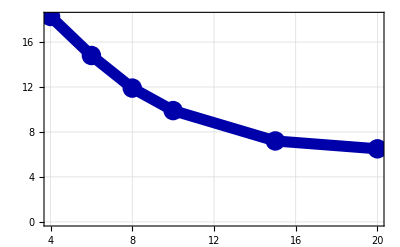

Part::partw: Part 6 of {{4.,10.},{6.,12.},{8.,32.},{10.,58.},{15.,23.}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

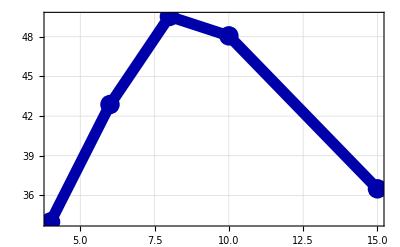

{{4.,26.1364},{6.,28.8375},{8.,30.7167},{10.,28.9833},{15.,21.85}}

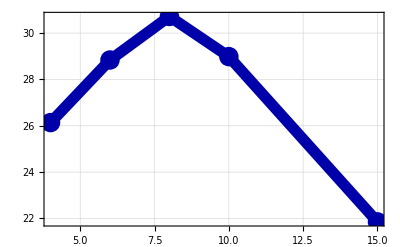

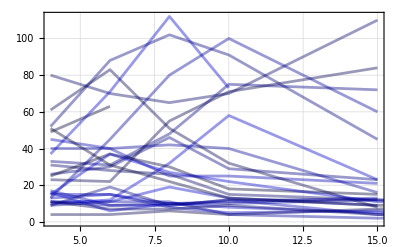

```mathematica
prnaTA1=rnaTA1//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
AvgrnaTA1=Cases[Table[Mean[Cases[rnaTA1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgrnaTA1=AvgrnaTA1//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
prnaTA2=rnaTA2//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
AvgrnaTA2=Cases[Table[Mean[Cases[rnaTA2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgrnaTA2=AvgrnaTA2//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgrnaTA=Table[Mean[{AvgrnaTA2[[i]],AvgrnaTA1[[i]]}],{i,1,Length@AvgrnaTA2,1}]
ptotalAvgrnaTA=totalAvgrnaTA//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
prnaTA = Show[prnaTA2,prnaTA1]
```

```mathematica
prnaTL2=rnaTL2//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgrnaTL2=Cases[Table[Mean[Cases[rnaTL2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgrnaTL2=AvgrnaTL2//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
prnaTL = Show[prnaTL2]
```

-Graphics-

Part::partw: Part 6 of {{4.,91.},{6.,101.},{8.,},{10.,},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

-Graphics-

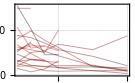

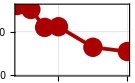

Part::partw: Part 6 of {{4.,13.},{6.,17.},{8.,18.},{10.,7.},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

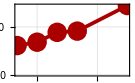

{{4.,36.3763},{6.,36.4056},{8.,34.2813},{10.,35.0192},{15.,38.5625}}

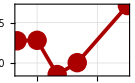

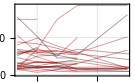

```mathematica
prnaNT1=rnaNT1//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgrnaNT1=Cases[Table[Mean[Cases[rnaNT1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgrnaNT1=AvgrnaNT1//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
prnaNT2=rnaNT2//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
AvgrnaNT2=Cases[Table[Mean[Cases[rnaNT2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgrnaNT2=AvgrnaNT2//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgrnaNT=Table[Mean[{AvgrnaNT2[[i]],AvgrnaNT1[[i]]}],{i,1,Length@AvgrnaNT2,1}]
ptotalAvgrnaNT=totalAvgrnaNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
prnaNT = Show[prnaNT2,prnaNT1]
```

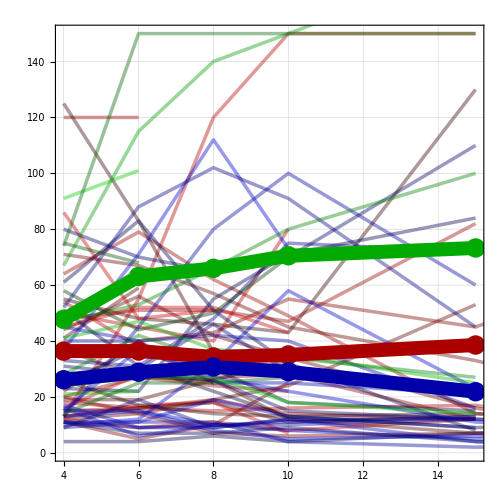

```mathematica
Show[prnaNT,prnaTA,prnaTL,ptotalAvgrnaNT,ptotalAvgrnaTA,pAvgrnaTL2,AspectRatio->1]
```

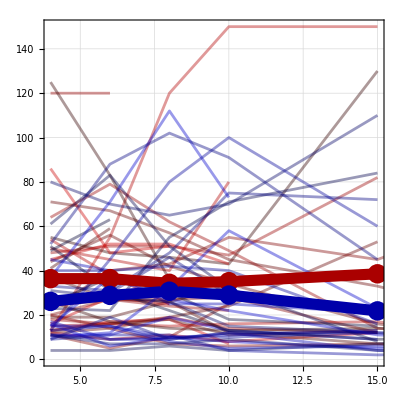

```mathematica
Show[prnaNT,prnaTA,ptotalAvgrnaNT,ptotalAvgrnaTA,PlotRange->{{4,15},{0,150}},AspectRatio->1]
```

#### %Translation :

```mathematica
ptransTA1=transTA1//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtransTA1=Cases[Table[Mean[Cases[transTA1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtransTA1=AvgtransTA1//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptransTA2=transTA2//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtransTA2=Cases[Table[Mean[Cases[transTA2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtransTA2=AvgtransTA2//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgtransTA=Table[Mean[{AvgtransTA2[[i]],AvgtransTA1[[i]]}],{i,1,Length@AvgtransTA2,1}];
ptotalAvgtransTA=totalAvgtransTA//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptransTA = Show[ptransTA2,ptransTA1]
```

-Graphics-

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,0.1},{6.,0.416667},{8.,0.15625},{10.,0.137931},{15.,0.0434783}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

-Graphics-

-Graphics-

```mathematica
ptransTL=transTL2//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtransTL2=Cases[Table[Mean[Cases[transTL2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2]
pAvgtransTL2=AvgtransTL2//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

Part::partw: Part 6 of {{4.,0.901099},{6.,0.970297},{8.,},{10.,},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

{{4.,0.556632},{6.,0.565412},{8.,0.458124},{10.,0.247129},{15.,0.145635}}

-Graphics-

```mathematica
ptransNT1=transNT1//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtransNT1=Cases[Table[Mean[Cases[transNT1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtransNT1=AvgtransNT1//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptransNT2=transNT2//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtransNT2=Cases[Table[Mean[Cases[transNT2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtransNT2=AvgtransNT2//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgtransNT=Table[Mean[{AvgtransNT2[[i]],AvgtransNT1[[i]]}],{i,1,Length@AvgtransNT2,1}]
ptotalAvgtransNT=totalAvgtransNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptransNT = Show[ptransNT1,ptransNT2]
```

-Graphics-

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,0.692308},{6.,0.647059},{8.,0.611111},{10.,0.571429},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

{{4.,0.749776},{6.,0.769071},{8.,0.774227},{10.,0.710656},{15.,0.401452}}

-Graphics-

-Graphics-

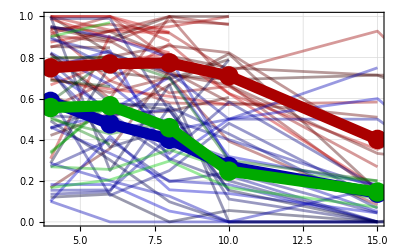

```mathematica
Show[ptransNT,ptransTA,ptransTL,ptotalAvgtransNT,ptotalAvgtransTA,pAvgtransTL2,PlotRange->{{4,15},{0,1}}]
```

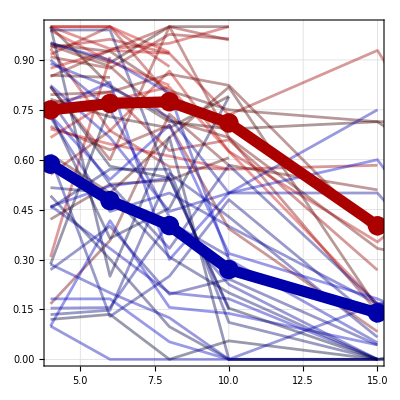

```mathematica
Show[ptransNT,ptransTA,ptotalAvgtransNT,ptotalAvgtransTA,PlotRange->{{4,15},{0,1}},AspectRatio->1]
```

#### # Tethered :

```mathematica
ptethTA1=tethTA1//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtethTA1=Cases[Table[Mean[Cases[tethTA1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethTA1=AvgtethTA1//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptethTA2=tethTA2//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtethTA2=Cases[Table[Mean[Cases[tethTA2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethTA2=AvgtethTA2//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgtethTA=Table[Mean[{AvgtethTA2[[i]],AvgtethTA1[[i]]}],{i,1,Length@AvgtethTA2,1}]
ptotalAvgtethTA=totalAvgtethTA//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
Show[ptethTA2,ptethTA1]
```

-Graphics-

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,2.},{6.,5.},{8.,5.},{10.,15.},{15.,17.}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

{{4.,11.0833},{6.,16.3176},{8.,19.4625},{10.,16.0333},{15.,10.9214}}

-Graphics-

-Graphics-

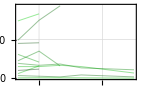

Part::partw: Part 6 of {{4.,89.},{6.,100.},{8.,},{10.,},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

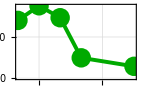

```mathematica
ptethTL=tethTL2//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtethTL=Cases[Table[Mean[Cases[tethTL2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethTL=AvgtethTL//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

```mathematica
ptethNT1=tethNT1//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtethNT1=Cases[Table[Mean[Cases[tethNT1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethNT1=AvgtethNT1//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptethNT2=tethNT2//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
AvgtethNT2=Cases[Table[Mean[Cases[tethNT2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethNT2=AvgtethNT2//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgtethNT=Table[Mean[{AvgtethNT2[[i]],AvgtethNT1[[i]]}],{i,1,Length@AvgtethNT2,1}]
ptotalAvgtethNT=totalAvgtethNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptethNT = Show[ptethNT2,ptethNT1]
```

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,1.},{6.,1.},{8.,1.},{10.,1.},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

{{4.,0.208333},{6.,0.227273},{8.,0.227273},{10.,0.227273},{15.,1.25}}

-Graphics-

-Graphics-

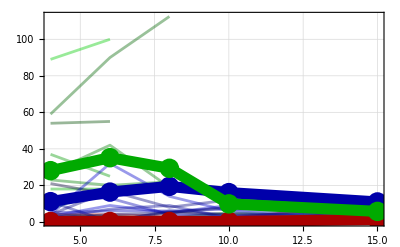

```mathematica
Show[ptethTL,ptethNT,ptethTA1,ptotalAvgtethNT,ptotalAvgtethTA,pAvgtethTL]
```

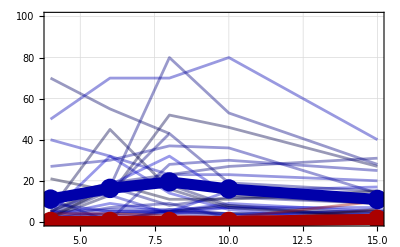

```mathematica
Show[ptethTA1,ptethTA2,ptethNT1,ptethNT2,ptotalAvgtethNT,ptotalAvgtethTA,PlotRange->{{4,15},{0,100}}]
```

#### % cy3 accumulation :

```mathematica
paccumTA1=accumTA1//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumTA1=Cases[Table[Mean[Cases[accumTA1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethTA1=AvgaccumTA1//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumTA2=accumTA2//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumTA2=Cases[Table[Mean[Cases[accumTA2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumTA2=AvgaccumTA2//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumTA3=accumTA3//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumTA3=Cases[Table[Mean[Cases[accumTA3[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethTA3=AvgaccumTA3//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgaccumTA=Table[Mean[{AvgaccumTA2[[i]],AvgaccumTA3[[i]],AvgaccumTA1[[i]]}],{i,1,Length@AvgaccumTA2,1}]
ptotalAvgaccumTA=totalAvgaccumTA//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.015]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumTA=Show[paccumTA3,paccumTA2,paccumTA1]
```

-Graphics-

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.05}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,0.05},{6.,0.},{8.,0.},{10.,0.},{15.,0.}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

{{4.,0.0789015},{6.,0.0812821},{8.,0.0864286},{10.,0.0996978},{15.,0.137201}}

-Graphics-

-Graphics-

```mathematica
StandardDeviation/@{AvgaccumTA1,AvgaccumTA2,AvgaccumTA3}
```

{{5.99166,0.0200859},{4.219,0.078208},{4.219,0.0131172}}

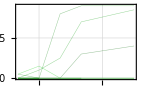

Part::partw: Part 6 of {{4.,0.},{6.,0.},{8.,},{10.,},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

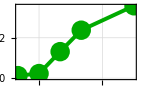

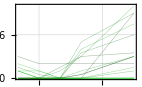

Part::partw: Part 6 of {{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

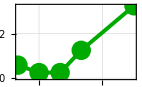

{{4.,0.0354167},{6.,0.0238636},{8.,0.078125},{10.,0.18125},{15.,0.341667}}

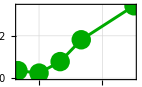

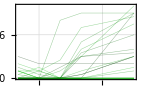

```mathematica
paccumTL2=accumTL2//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumTL2=Cases[Table[Mean[Cases[accumTL2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumTL2=AvgaccumTL2//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumTL3=accumTL3//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumTL3=Cases[Table[Mean[Cases[accumTL3[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumTL3=AvgaccumTL3//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgaccumTL=Table[Mean[{AvgaccumTL2[[i]],AvgaccumTL3[[i]]}],{i,1,Length@AvgaccumTA2,1}]
ptotalAvgaccumTL=totalAvgaccumTL//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.015]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumTL = Show[paccumTL3,paccumTL2]
```

```mathematica
paccumNT1=accumNT1//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumNT1=Cases[Table[Mean[Cases[accumNT1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumNT1=AvgaccumNT1//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumNT2=accumNT2//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
AvgaccumNT2=Cases[Table[Mean[Cases[accumNT2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumNT2=AvgaccumNT2//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumNT3=accumNT3//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumNT3=Cases[Table[Mean[Cases[accumNT1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumNT3=AvgaccumNT3//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgaccumNT=Table[Mean[{AvgaccumNT2[[i]],AvgaccumNT3[[i]],AvgaccumNT1[[i]]}],{i,1,Length@AvgaccumNT2,1}]
ptotalAvgaccumNT=totalAvgaccumNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.015]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumNT = Show[paccumNT2,paccumNT1,paccumNT3]
```

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,0.1},{6.,0.1},{8.,0.},{10.,0.},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

-Graphics-

-Graphics-

{{4.,0.0501684},{6.,0.0823232},{8.,0.172054},{10.,0.280808},{15.,0.499632}}

-Graphics-

-Graphics-

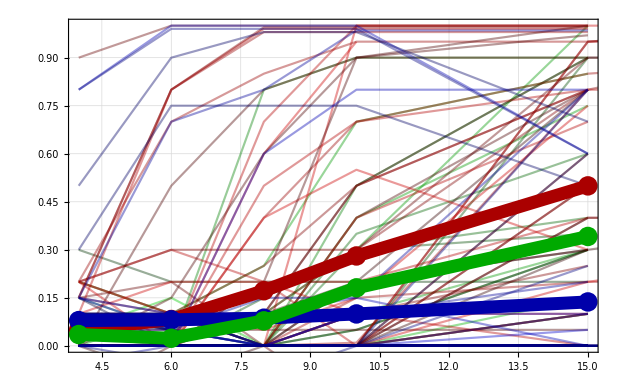

```mathematica
Show[paccumTL,paccumNT,paccumTA,ptotalAvgaccumNT,ptotalAvgaccumTA,ptotalAvgaccumTL,PlotRange->{{4,15},{0,1}}]
```

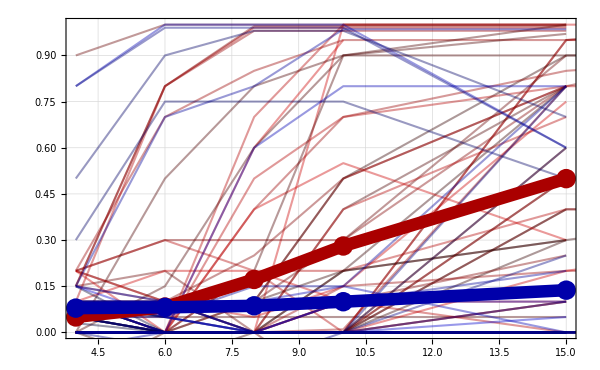

```mathematica
Show[paccumNT,paccumTA,ptotalAvgaccumNT,ptotalAvgaccumTA,PlotRange->{{4,15},{0,1}},ImageSize->600]
```

```mathematica
(*   standardError[ts_]:=StandardDeviation[ts]/Sqrt[ts["PathLength"]]
```

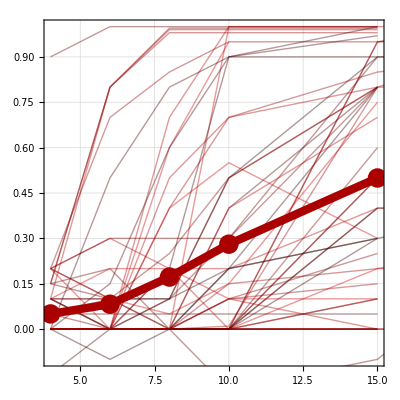

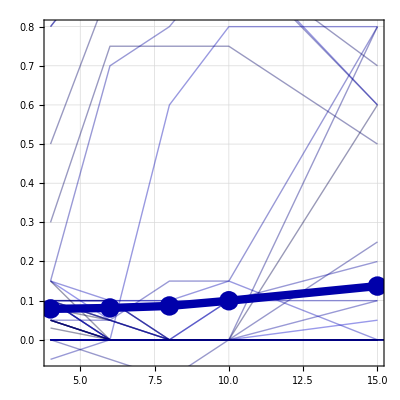

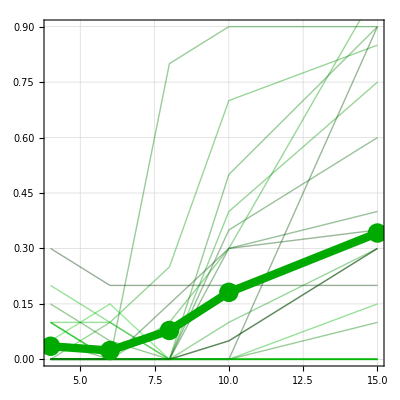

```mathematica
Show[paccumNT2,paccumNT1,paccumNT3,ptotalAvgaccumNT, PlotRange->{{4,15},{-.1,1}},AspectRatio->1]
Show[paccumTA2,paccumTA1,paccumTA3,ptotalAvgaccumTA, AspectRatio->1]
Show[paccumTL2,paccumTL3,ptotalAvgaccumTL, AspectRatio->1]
```

```mathematica
devAccumTA = StandardDeviation/@Table[{AvgaccumTA1[[j,2]],AvgaccumTA2[[j,2]],AvgaccumTA3[[j,2]]},{j,1,Length@AvgaccumTA2,1}]
devAccumNT = StandardDeviation/@Table[{AvgaccumNT1[[j,2]],AvgaccumNT2[[j,2]],AvgaccumNT3[[j,2]]},{j,1,Length@AvgaccumNT2,1}]
devAccumTL = StandardDeviation/@Table[{AvgaccumTL2[[j,2]],AvgaccumTL3[[j,2]]},{j,1,Length@AvgaccumTL2,1}]
```

{0.0412543,0.0577555,0.0764085,0.0869484,0.129914}

{0.0237647,0.0594846,0.0820829,0.10541,0.102522}

{0.0324091,0.00160706,0.0751301,0.0795495,0.0235702}

```mathematica
errorAccumTA = ;
errorAccumNT = ;
errorAccumTL = ;
```

## Graphs: Accumulation: Removing cells with HIGH early accumulation

```mathematica
NTdata = Join[myNT1, myNT2];
TAdata = Join[myTA1, myTA2];
TLdata = Join[myTL2];
```

```mathematica
(*
m = 20
n = 80
o = 3
NTdataL=Cases[NTdata,x_/;x[[2,1,o,2]]<m];
NTdataM=Cases[NTdata,x_/;m≤x[[2,1,o,2]]≤n];
NTdataH=Cases[NTdata,x_/;n<x[[2,1,o,2]]];
TAdataL=Cases[TAdata,x_/;x[[2,1,o,2]]<m];
TAdataM=Cases[TAdata,x_/;m≤x[[2,1,o,2]]≤n];
TAdataH=Cases[TAdata,x_/;n<x[[2,1,o,2]]];
TLdataL=Cases[TLdata,x_/;x[[2,1,o,2]]<m];
TLdataM=Cases[TLdata,x_/;m≤x[[2,1,o,2]]≤n];
TLdataH=Cases[TLdata,x_/;n<x[[2,1,o,2]]];
*)
```

```mathematica
rmNTdata = NTdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTLdata = TLdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTAdata = TAdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
```

```mathematica
(*0
m = 20;
n = 60;
o = 4;
p=2;
NTdata0= rmNTdata//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
NTdataL= rmNTdata//Cases[#,x_/; x⟦p,1,o,2⟧< m]&;
NTdataM= rmNTdata//Cases[#,x_/; m≤ x⟦p,1,o,2⟧≤n]&;
NTdataH= rmNTdata//Cases[#,x_/; n< x⟦p,1,o,2⟧]&;
TAdata0= rmTAdata//Cases[#,x_/;  Head[x⟦p,1,o,2⟧]== String]&;
TAdataL=TAdata//Cases[#,x_/;  x⟦p,1,o,2⟧< m]&;
TAdataM= rmTAdata//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤ n]&;
TAdataH= rmTAdata//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
TLdata0= rmTLdata//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
TLdataL=TLdata//Cases[#,x_/;   x⟦p,1,o,2⟧<m]&;
TLdataM= rmTLdata//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤n]&;
TLdataH= rmTLdata//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
```

```mathematica
(*
NTdata0= rmNTdata/.""->0.//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
NTdataL= rmNTdata/.""->0.//Cases[#,x_/; x⟦p,1,o,2⟧< m]&;
NTdataM= rmNTdata/.""->0.//Cases[#,x_/; m≤ x⟦p,1,o,2⟧≤n]&;
NTdataH= rmNTdata/.""->0.//Cases[#,x_/; n< x⟦p,1,o,2⟧]&;
TAdata0= rmTAdata/.""->0.//Cases[#,x_/;  Head[x⟦p,1,o,2⟧]== String]&;
TAdataL=TAdata/.""->0.//Cases[#,x_/;  x⟦p,1,o,2⟧< m]&;
TAdataM= rmTAdata/.""->0.//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤ n]&;
TAdataH= rmTAdata/.""->0.//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
TLdata0= rmTLdata/.""->0.//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
TLdataL=TLdata/.""->0.//Cases[#,x_/;   x⟦p,1,o,2⟧<m]&;
TLdataM= rmTLdata/.""->0.//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤n]&;
TLdataH= rmTLdata/.""->0.//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
*)
```

```mathematica
NTdata[[5,2,1,2,2]]
```

44.

```mathematica
NTdata[[All,2,1,o,2]]
```

Part::pkspec1: The expression o cannot be used as a part specification.

```mathematica
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
```

TA  31   inc 4   lo 10   med 11   hi 2

NT  31   inc 3   lo 9   med 15   hi 2

TL  13   inc 4   lo 0    med 5    hi 3

### Graphs...

#### RNA :

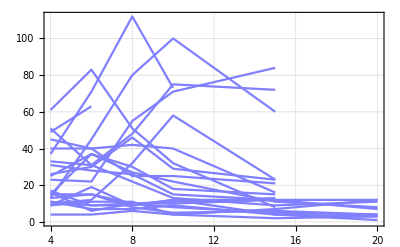
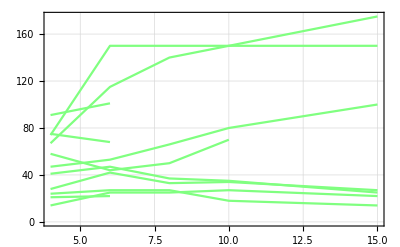
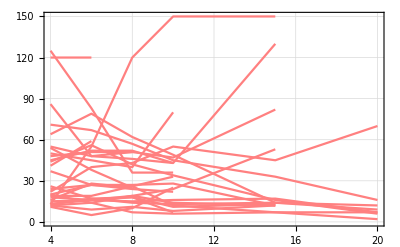

```mathematica
prnaTA = 
rmTAdata[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All, ImageSize->400]&;
prnaTL = 
rmTLdata[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
prnaNT = 
rmNTdata[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
Row[{
prnaTA, prnaTL, prnaNT
}]
```

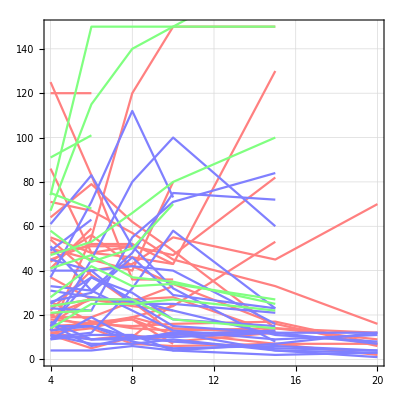

```mathematica
Show[prnaNT,prnaTA,prnaTL,AspectRatio->1]
```

#### %Translation :

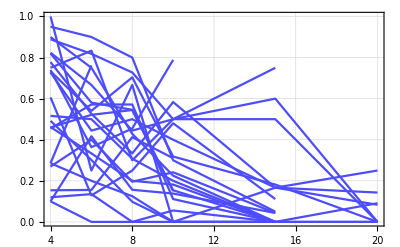
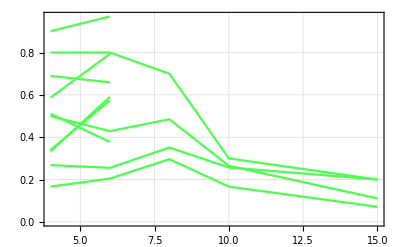
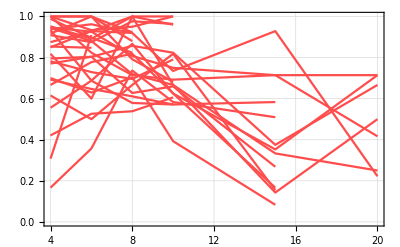

```mathematica
ptransTL=rmTLdata[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
ptransNT=rmNTdata[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
ptransTA=rmTAdata[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
Row[{
ptransTA, ptransTL, ptransNT
}]
```

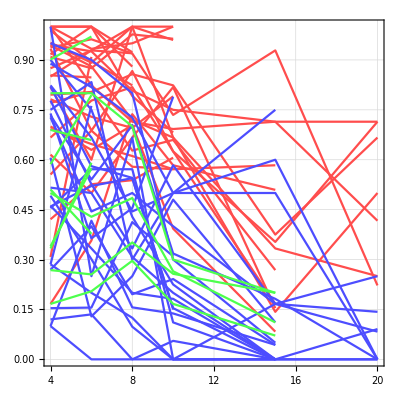

```mathematica
Show[ptransNT,ptransTA,ptransTL,AspectRatio->1]
```

#### Cy3 accumulation :

Make lists of {time,accumulation} for each of the 2 or 3 datasets, removing any cells with >20% accumulation at the first time point!

```mathematica
rmNT1 = myNT1//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&//#⟦All,4⟧&;
rmTA1 = myTA1//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&//#⟦All,4⟧&;
rmNT2 = myNT2//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&//#⟦All,4⟧&;
rmTL2 = myTL2//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&//#⟦All,4⟧&;
rmTA2 = myTA2//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&//#⟦All,4⟧&;
rmNT3 = myNT3//Cases[#,x_/; x⟦2,1,2,2⟧≤ .2]&//#⟦All,2⟧&;
rmTL3 = myTL3//Cases[#,x_/; x⟦2,1,2,2⟧≤ .2]&//#⟦All,2⟧&;
rmTA3 = myTA3//Cases[#,x_/; x⟦2,1,2,2⟧≤ .2]&//#⟦All,2⟧&;
```

Make SUPER list of {time,accumulation} per each treatment

```mathematica
myNTaccum = Join[rmNTdata⟦All,4,1,All⟧,Flatten[rmNT3⟦All⟧,1]];
Dimensions[myNTaccum]
```

{43}

```mathematica
myTAaccum = Join[rmTAdata⟦All,4,1,All⟧,Flatten[rmTA3⟦All⟧,1]];
Dimensions[myTAaccum]
```

{46}

```mathematica
myTLaccum = Join[rmTLdata⟦All,4,1,All⟧,Flatten[rmTL3⟦All⟧,1]];
Dimensions[myTLaccum]
```

{25,6,2}

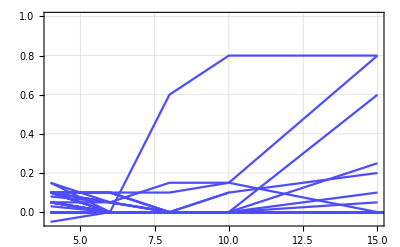
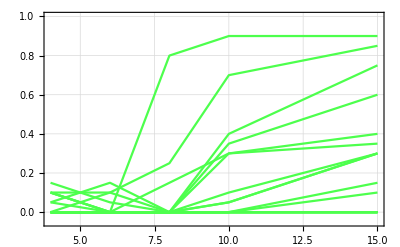
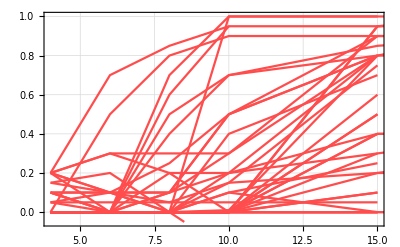

```mathematica
paccumTL=myTLaccum[[All,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",ImageSize->400, PlotRange -> {{4,15},{-.05, 1}}]&;
paccumNT=myNTaccum[[All,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange -> {{4,15},{-.05, 1}},ImageSize->400]&;
paccumTA=myTAaccum[[All,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange -> {{4,15},{-.05, 1}},ImageSize->400]&;
Row[{
paccumTA, paccumTL, paccumNT
}]
```

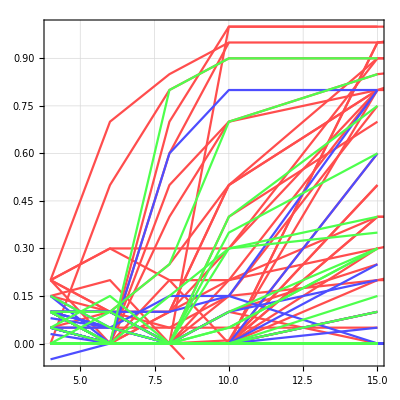

```mathematica
Show[paccumNT,paccumTA,paccumTL,AspectRatio->1, PlotRange -> {{4,15},{-.05, 1}}]
```

#### Now, only plot the averages

-> take the average of ALL data
-> find the SEM error of the data sets

```mathematica
mytimes = myTAaccum[[1,2;;6,1]];
TAaccum = myTAaccum //Cases[#,x_/; -1<x⟦6,2⟧<2]& ;
TLaccum = myTLaccum //Cases[#,x_/; -1<x⟦6,2⟧<2]& ;
NTaccum = myNTaccum //Cases[#,x_/; -1<x⟦6,2⟧<2]& ;
(*This gets rid of non-numerical entries in your lists*)
```

```mathematica
avgTAaccum = TAaccum //Transpose[#[[All,2;;6,2]]]&//Mean/@#&//{mytimes,#}&//Transpose;
avgTLaccum = TLaccum //Transpose[#[[All,2;;6,2]]]&//Mean/@#&//{mytimes,#}&//Transpose;
avgNTaccum = NTaccum //Transpose[#[[All,2;;6,2]]]&//Mean/@#&//{mytimes,#}&//Transpose;
(*
This is now a list of the averages of ALL the cells 
*)
```

```mathematica
Row[{
"Total cells" ,"    ",
"Cells with >=20%accum at time 15h","    ","Ratio of cells with >=20%accum at time 15h"}]
Row[{
Length@TAaccum ,"    ",
overTAaccum = TAaccum //Cases[#,x_/;x⟦6,2⟧>=.2]& //Length,"     ",N[overTAaccum/Length@TAaccum]}]
Row[{Length@TLaccum ,"    ",
overTLaccum = TLaccum //Cases[#,x_/;x⟦6,2⟧>=.2]& //Length,"    ",N[overTLaccum/Length@TLaccum]}]
Row[{Length@NTaccum ,"    ",
overNTaccum = NTaccum //Cases[#,x_/;x⟦6,2⟧>=.2]& //Length,"    ",N[overNTaccum/Length@NTaccum]}
]
(*
This summarizes the cells with (1) less than 20% accum (2) more than 20% accum (3) total % of cells with accumulation
*)
```

Total cells    Cells with >=20%accum at time 15h    Ratio of cells with >=20%accum at time 15h

41    5     0.121951

19    9    0.473684

39    28    0.717949

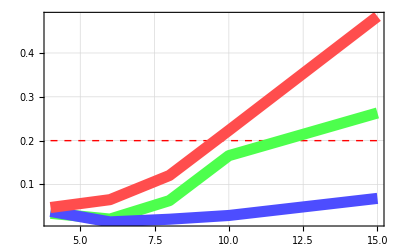

```mathematica
(*
Now graph averages... 
*)
pavgTLaccum=avgTLaccum//ListPlot[#,PlotStyle->{Lighter[Green,.3], Thickness[.02]},Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
pavgTAaccum=avgTAaccum//ListPlot[#,PlotStyle->{Lighter[Blue,.3],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
pavgNTaccum=avgNTaccum//ListPlot[#,PlotStyle->{Lighter[Red,.3],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400]&;
line = ListPlot[{{4,.2},{15,.2}},PlotStyle->{Red,Thickness[0.0025], Dashed},Joined->True,PlotTheme->"Detailed",PlotRange->All,ImageSize->400];
Show[line,pavgTLaccum,pavgTAaccum,pavgNTaccum, PlotRange->All]
```

```mathematica
(*
Now calculate error at each time point. 
The error is the deviation of the averages...  
*)
```

```mathematica
a = Transpose[myNT2[[All,4,1,2;;6,2]]]
```

{{0.1,0.,0.,,,0.05,0.,0.,0.,0.,0.1,0.,0.},{0.1,0.,0.,,,0.05,0.,0.,0.,0.,0.,0.,0.},{0.,0.7,0.,,,0.05,0.,0.,0.,0.1,0.,0.,0.},{0.,1.,0.,,,0.05,0.2,0.,0.,0.5,0.,0.,0.},{,1.,0.,,,0.05,0.8,0.,,0.8,0.,0.4,}}

```mathematica
Table[a[[i]]//Cases[#,x_/; x ≠ ""]& ,{i,1,5,1}]
```

{{0.1,0.,0.,0.05,0.,0.,0.,0.,0.1,0.,0.},{0.1,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.},{0.,0.7,0.,0.05,0.,0.,0.,0.1,0.,0.,0.},{0.,1.,0.,0.05,0.2,0.,0.,0.5,0.,0.,0.},{1.,0.,0.05,0.8,0.,0.8,0.,0.4}}

```mathematica
(*
Remove all the zeros out of NT accumulation data {{data at time 1},{data at time 2}, {...}}
*)
accumNT1trans = Transpose[myNT1[[All,4,1,2;;6,2]]];rmNT1 =Table[accumNT1trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmNT1
accumNT2trans = Transpose[myNT2[[All,4,1,2;;6,2]]];rmNT2 =Table[accumNT2trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmNT2
accumNT3trans = Transpose[myNT3[[All,2,1,2;;6,2]]];rmNT3 =Table[accumNT3trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmNT3
```

{{0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.3,0.,0.3,0.2,0.1,0.,0.,0.,0.7,0.,0.,0.5,0.,0.,0.,0.,0.},{0.,0.2,0.,0.3,0.,0.,0.,0.6,0.2,0.85,0.,0.,0.8,0.1,0.,0.5,0.4,0.},{1.,0.2,0.15,0.3,-0.2,0.,0.,0.95,0.,0.95,0.,0.,0.9,0.5,0.,0.7,0.7,0.},{1.,0.4,0.2,0.8,-0.1,0.4,0.3,0.95,0.95,0.95,0.,0.9,0.9,0.2,0.8,0.85,0.}}

{18,18,18,18,17}

{{0.1,0.,0.,0.05,0.,0.,0.,0.,0.1,0.,0.},{0.1,0.,0.,0.05,0.,0.,0.,0.,0.,0.,0.},{0.,0.7,0.,0.05,0.,0.,0.,0.1,0.,0.,0.},{0.,1.,0.,0.05,0.2,0.,0.,0.5,0.,0.,0.},{1.,0.,0.05,0.8,0.,0.8,0.,0.4}}

{11,11,11,11,8}

{{0.,0.1,0.05,0.15,0.1,0.2,0.,0.,0.1,0.,0.05,0.,0.,0.},{0.,0.,0.,0.1,0.1,0.1,0.,0.,0.,0.,0.1,0.,0.,0.},{0.,0.,0.,0.1,0.1,0.05,0.,0.,0.,0.,0.25,0.,0.,0.},{0.,0.,0.1,0.3,0.2,0.15,0.,0.,0.,0.1,0.5,0.,0.4,0.01},{0.,0.5,0.25,0.9,0.3,0.75,0.6,0.5,0.1,0.,0.8,0.1,0.7,0.8}}

{14,14,14,14,14}

```mathematica
(*
Remove all the zeros out of TA accumulation data {{data at time 1},{data at time 2}, {...}}
*)
accumTA1trans = Transpose[myTA1[[All,4,1,2;;6,2]]];rmTA1 =Table[accumTA1trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmTA1
accumTA2trans = Transpose[myTA2[[All,4,1,2;;6,2]]];rmTA2 =Table[accumTA2trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmTA2
accumTA3trans = Transpose[myTA3[[All,2,1,2;;6,2]]];rmTA3 =Table[accumTA3trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmTA3
```

{{0.,0.1,0.,0.1,0.,0.,0.,0.1,0.,0.1,0.1},{0.,0.1,0.,0.,0.,0.,0.1,0.,0.,0.1},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{11,10,10,10,10}

{{0.,0.,-0.05,0.05,0.,0.,0.03,0.1,0.2,0.1,0.3,0.05,0.08,0.15,0.,0.05},{0.,0.,0.,0.,0.,0.,0.,0.1,0.05,0.75,0.,0.05,0.05,0.,0.05},{0.,0.,0.,0.,0.,0.,0.,0.1,0.,0.75,0.,0.,0.6,0.15},{0.,0.,0.,0.,0.,0.,0.,0.15,0.,0.75,0.,0.1,0.8,0.15},{0.05,0.,0.1,0.,0.6,0.,0.,0.25,0.5,0.,0.8,0.8}}

{16,15,14,14,12}

{{0.05,0.,0.05,0.,0.,0.,0.,0.1,0.1,0.,0.15,0.1,0.,0.,0.05,0.,0.,0.1,0.05,0.1},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.05},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{20,20,20,20,20}

```mathematica
(*
Remove all the zeros out of TL accumulation data {{data at time 1},{data at time 2}, {...}}
*)
accumTL2trans = Transpose[myTL2[[All,4,1,2;;6,2]]];rmTL2 =Table[accumTL2trans[[i]]//Cases[#,x_/; NumericQ[x]]&,{i,1,5,1}]
Length/@rmTL2
accumTL3trans = Transpose[myTL3[[All,2,1,2;;6,2]]];rmTL3 =Table[accumTL3trans[[i]]//Cases[#,x_/; x≠ ""]&,{i,1,5,1}]
Length/@rmTL3
```

{{0.,0.,0.,0.,0.,0.,0.,0.05,0.,0.05,0.,0.05},{0.,0.,0.1,0.,0.,0.,0.,0.15,0.,0.,0.},{0.25,0.8,0.,0.,0.,0.,0.,0.},{0.7,0.9,0.,0.,0.,0.,0.,0.3},{0.85,0.9,0.,0.,0.,0.4}}

{12,11,8,8,6}

{{0.,0.,0.,0.,0.1,0.1,0.1,0.15,0.,0.,0.,0.1,0.},{0.,0.,0.,0.,0.,0.1,0.,0.05,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.15,0.,0.,0.},{0.,0.4,0.,0.35,0.,0.,0.1,0.,0.05,0.3,0.05,0.,0.},{0.,0.75,0.,0.6,0.,0.,0.3,0.1,0.3,0.35,0.3,0.,0.15}}

{13,13,13,13,13}

```mathematica
(*
Now that you have these 3 data sets, calc averages of each... 
*)
```

```mathematica
Transpose[{Mean/@rmNT1,Mean/@rmNT2,Mean/@rmNT3}]
Transpose[{Mean/@rmTA1,Mean/@rmTA2,Mean/@rmTA3}]
Transpose[{Mean/@rmTL2,Mean/@rmTL3}]
```

{{0.0638889,0.06625,0.0535714},{0.116667,0.07,0.0285714},{0.219444,0.114286,0.0357143},{0.341667,0.139286,0.125714},{0.558824,0.258333,0.45}}

{{0.0454545,0.06625,0.0425},{0.03,0.07,0.005},{0.,0.114286,0.},{0.,0.139286,0.005},{0.,0.258333,0.01}}

{{0.0125,0.0423077},{0.0227273,0.0115385},{0.13125,0.0115385},{0.2375,0.0961538},{0.358333,0.219231}}

```mathematica
tempList = Transpose[rmNT1[[All, 1,2;;All,2]]];
```

```mathematica
tempList[[1,2]]
```

0.2

```mathematica
Table[Cases[rmNT3[[All,i]],x_/;NumericQ[x⟦2⟧]],{i,2,6,1}]
```

Part::partw: Part 2 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{},{},{},{},{}}

```mathematica
tempAvt = Cases[Table[Mean[Cases[rmNT3[[All,i]],x_/;NumericQ[x[[2]]]]],{i,2,6,1}],x_/;Length[x]==2]
```

Part::partw: Part 2 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 2⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of {{{accum,Cy3 accum},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{}

```mathematica
Cases[tempList, x_/;Table[Table[x[[i,j]]/= "",{j,1,Length@tempList[[1]],1}],{i,1,Length@tempList,1}]]
```

Part::partd: Part specification {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.}⟦1,1⟧ is longer than depth of object.

Set::setps: {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.} in the part assignment is not a symbol.

Part::partd: Part specification {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.}⟦1,2⟧ is longer than depth of object.

Set::setps: {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.} in the part assignment is not a symbol.

Part::partd: Part specification {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.}⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Set::setps: {0.,0.2,0.,0.2,0.15,0.2,0.,0.2,0.,0.2,0.,0.,0.,0.,0.,0.,0.,0.} in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

{}

```mathematica
Cases[#,x_/;x⟦6,2⟧>.2]&
```

```mathematica
μNT1 = Mean/@rmNT1[[2;;All]]
```

{{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.3},{8.,0.2},{10.,0.2},{15.,0.4},{20.,0.4}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.15},{15.,0.2},{20.,0.2}},{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.3},{8.,0.3},{10.,0.3},{15.,0.8},{20.,0.95}},{{hours,Cy3 Accum (%)},{4.,0.15},{6.,0.2},{8.,0.},{10.,-0.2},{15.,-0.1},{20.,0.3}},{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.1},{8.,0.},{10.,0.},{15.,0.4},{20.,0.4}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.3},{20.,0.4}},{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.},{8.,0.6},{10.,0.95},{15.,},{20.,}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.2},{10.,0.},{15.,0.95},{20.,0.95}},{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.7},{8.,0.85},{10.,0.95},{15.,0.95},{20.,1.}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.95},{20.,1.}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.},{20.,0.}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.5},{8.,0.8},{10.,0.9},{15.,0.9},{20.,0.9}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.1},{10.,0.5},{15.,0.9},{20.,0.9}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.2},{20.,0.3}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.5},{10.,0.7},{15.,0.8},{20.,0.8}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.4},{10.,0.7},{15.,0.85},{20.,0.9}},{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.},{20.,0.}}}

```mathematica
Needs["ErrorBarPlots`"];
{μavgTLaccum,σNT}
```

{μavgTLaccum,σNT}

### Totals :

Binned by # RNA per cell at Frame 4 : <20,  20-80,  <80

TA  31   inc 4   lo 10   med 11   hi 2

NT  31   inc 3   lo 9   med 15   hi 2

TL  13   inc 4   lo 0    med 5    hi 3

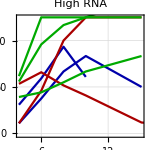
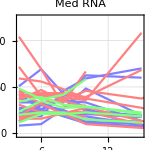
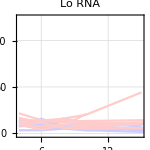

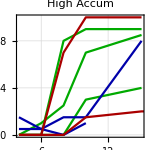
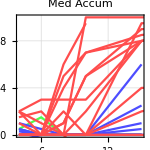
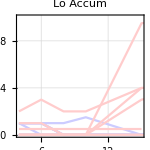

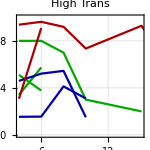
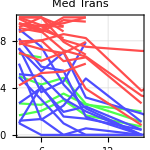

```mathematica
Row[{StringForm["Binned by # RNA per cell at Frame `` : <20,  20-80,  <80   ",o]}]
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
Row[{Show[prnaTAH,prnaNTH,prnaTLH,AspectRatio->1,PlotLabel->"High RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150],
Show[prnaTAM,prnaNTM,prnaTLM,AspectRatio->1,PlotLabel->"Med RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150],
Show[prnaTLL,prnaTAL,prnaNTL,prnaTLL,AspectRatio->1,PlotLabel->"Lo RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150]
}]
Row[{Show[paccumTLH,paccumTAH,paccumNTH,AspectRatio->1,PlotLabel->"High Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLM,paccumTAM,paccumNTM,AspectRatio->1,PlotLabel->"Med Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLL,paccumTAL,paccumNTL,AspectRatio->1,PlotLabel->"Lo Accum",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[ptransTLH,ptransTAH,ptransNTH,AspectRatio->1,PlotLabel->"High Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLM,ptransTAM,ptransNTM,AspectRatio->1,PlotLabel->"Med Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLL,ptransTAL,ptransNTL,AspectRatio->1,PlotLabel->"Lo Trans",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]

(*
Row[{"***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore!   "}]
*)
```

### Graph the %accumulation at 10h for HML w a scatter plot

```mathematica
accumNTL= Table[NTdataL[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataL,1}];
accumNTM= Table[NTdataM[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataM,1}];
accumNTH= Table[NTdataH[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataH,1}];accumTLL= Table[TLdataL[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataL,1}];
accumTLM= Table[TLdataM[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataM,1}];
accumTLH= Table[TLdataH[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataH,1}];
accumTAL= Table[TAdataL[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataL,1}];
accumTAM= Table[TAdataM[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataM,1}];
accumTAH= Table[TAdataH[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataH,1}];
```

```mathematica
accumTLall = Join[accumTLL, accumTLM, accumTLH];
accumTAall = Join[accumTAL, accumTAM, accumTAH];
accumNTall = Join[accumNTL, accumNTM, accumNTH];
```

#### % cy3 accumulation :

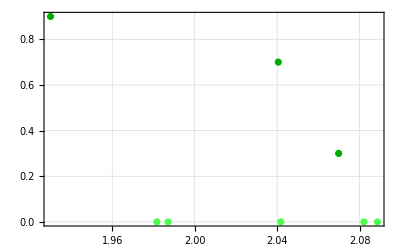

```mathematica
paccumTLL=accumTLL//ListPlot[#,PlotStyle->Lighter[Green,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=accumTLM//ListPlot[#,PlotStyle->Lighter[Green,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=accumTLH//ListPlot[#,PlotStyle->Darker[Green],PlotTheme->"Detailed",PlotRange->All]&;
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH,PlotRange-> All]
```

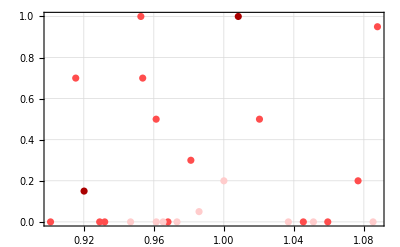

```mathematica
paccumNTL=accumNTL//ListPlot[#,PlotStyle->Lighter[Red,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=accumNTM//ListPlot[#,PlotStyle->Lighter[Red,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=accumNTH//ListPlot[#,PlotStyle->Darker[Red],PlotTheme->"Detailed",PlotRange->All]&;
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH, PlotRange-> {0,1}]
```

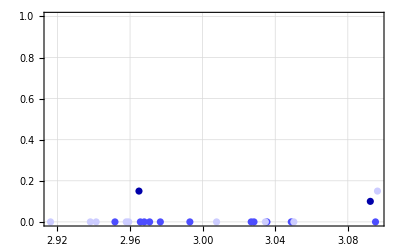

```mathematica
paccumTAL=accumTAL//ListPlot[#,PlotStyle->Lighter[Blue,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=accumTAM//ListPlot[#,PlotStyle->Lighter[Blue,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=accumTAH//ListPlot[#,PlotStyle->Darker[Blue],PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH,PlotRange-> {0,1}]
```

```mathematica
accumTLall
```

{{2.04175,0.},{1.98706,0.},{2.08865,0.},{2.08206,0.},{1.98164,0.},{2.04055,0.7},{1.93006,0.9},{2.06982,0.3}}

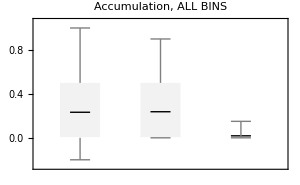
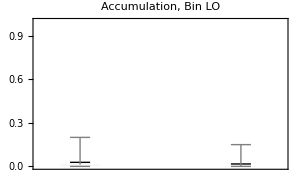
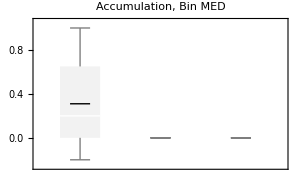
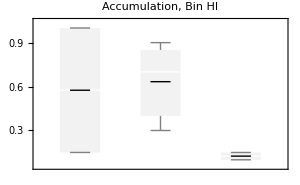

```mathematica
pBW = BoxWhiskerChart[{accumNTall⟦All,2⟧,accumTLall⟦All,2⟧,accumTAall⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, ALL BINS"];
pBWL = BoxWhiskerChart[{accumNTL⟦All,2⟧,accumTLL⟦All,2⟧,accumTAL⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, Bin LO", PlotRange -> {0,1}];
pBWM = BoxWhiskerChart[{accumNTM⟦All,2⟧,accumTLM⟦All,2⟧,accumTAM⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, Bin MED"];
pBWH = BoxWhiskerChart[{accumNTH⟦All,2⟧,accumTLH⟦All,2⟧,accumTAH⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, Bin HI"];
Row[{pBW, pBWL, pBWM, pBWH
}]
```

NT, TL, and TA accumulation% at 10h
The MEDIAN is represented as a black line. 
The MEAN of each is 0

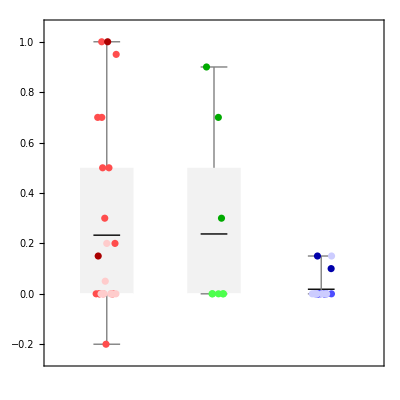

```mathematica
Row[{"NT, TL, and TA accumulation% at 10h
The MEDIAN is represented as a black line. 
The MEAN of each is 0"
}]
Row[{Show[pBW,paccumNT,paccumTL,paccumTA,AspectRatio->1,PlotRange->All  ]
}]
```

## Binning based on #RNA in cell at frame # (choose 2, 3, 4, 5, or 6)

```mathematica
NTdata = Join[myNT1, myNT2];
TAdata = Join[myTA1, myTA2];
TLdata = Join[myTL2];
```

```mathematica
(*
m = 20
n = 80
o = 3
NTdataL=Cases[NTdata,x_/;x[[2,1,o,2]]<m];
NTdataM=Cases[NTdata,x_/;m≤x[[2,1,o,2]]≤n];
NTdataH=Cases[NTdata,x_/;n<x[[2,1,o,2]]];
TAdataL=Cases[TAdata,x_/;x[[2,1,o,2]]<m];
TAdataM=Cases[TAdata,x_/;m≤x[[2,1,o,2]]≤n];
TAdataH=Cases[TAdata,x_/;n<x[[2,1,o,2]]];
TLdataL=Cases[TLdata,x_/;x[[2,1,o,2]]<m];
TLdataM=Cases[TLdata,x_/;m≤x[[2,1,o,2]]≤n];
TLdataH=Cases[TLdata,x_/;n<x[[2,1,o,2]]];
*)
```

```mathematica
rmNTdata = NTdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTLdata = TLdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTAdata = TAdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
```

```mathematica
m = 20;
n = 60;
o = 4;
p=2;
NTdata0= rmNTdata//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
NTdataL= rmNTdata//Cases[#,x_/; x⟦p,1,o,2⟧< m]&;
NTdataM= rmNTdata//Cases[#,x_/; m≤ x⟦p,1,o,2⟧≤n]&;
NTdataH= rmNTdata//Cases[#,x_/; n< x⟦p,1,o,2⟧]&;
TAdata0= rmTAdata//Cases[#,x_/;  Head[x⟦p,1,o,2⟧]== String]&;
TAdataL=TAdata//Cases[#,x_/;  x⟦p,1,o,2⟧< m]&;
TAdataM= rmTAdata//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤ n]&;
TAdataH= rmTAdata//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
TLdata0= rmTLdata//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
TLdataL=TLdata//Cases[#,x_/;   x⟦p,1,o,2⟧<m]&;
TLdataM= rmTLdata//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤n]&;
TLdataH= rmTLdata//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
```

```mathematica
(*
NTdata0= rmNTdata/.""->0.//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
NTdataL= rmNTdata/.""->0.//Cases[#,x_/; x⟦p,1,o,2⟧< m]&;
NTdataM= rmNTdata/.""->0.//Cases[#,x_/; m≤ x⟦p,1,o,2⟧≤n]&;
NTdataH= rmNTdata/.""->0.//Cases[#,x_/; n< x⟦p,1,o,2⟧]&;
TAdata0= rmTAdata/.""->0.//Cases[#,x_/;  Head[x⟦p,1,o,2⟧]== String]&;
TAdataL=TAdata/.""->0.//Cases[#,x_/;  x⟦p,1,o,2⟧< m]&;
TAdataM= rmTAdata/.""->0.//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤ n]&;
TAdataH= rmTAdata/.""->0.//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
TLdata0= rmTLdata/.""->0.//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
TLdataL=TLdata/.""->0.//Cases[#,x_/;   x⟦p,1,o,2⟧<m]&;
TLdataM= rmTLdata/.""->0.//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤n]&;
TLdataH= rmTLdata/.""->0.//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
*)
```

```mathematica
NTdata[[5,2,1,2,2]]
```

44.

```mathematica
NTdata[[All,2,1,o,2]]
```

{25.,15.,62.,43.,42.,26.,14.,52.,40.,,10.,57.,,36.,51.,25.,24.,7.,18.,120.,19.,,,18.,46.,11.,,51.,27.,19.,26.}

```mathematica
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
```

TA  31   inc 4   lo 10   med 11   hi 2

NT  31   inc 3   lo 9   med 15   hi 2

TL  13   inc 4   lo 0    med 5    hi 3

### Graphs...

#### RNA :

```mathematica
prnaTAL = 
TAdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAM = 
TAdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAH = 
TAdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
```

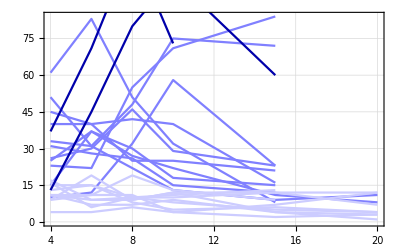

```mathematica
prnaTA = Show[prnaTAM,prnaTAL, prnaTAH]
```

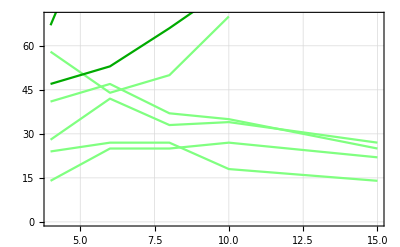

```mathematica
prnaTLL = 
TLdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLM = 
TLdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLH = 
TLdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTL = Show[prnaTLM,prnaTLL, prnaTLH]
```

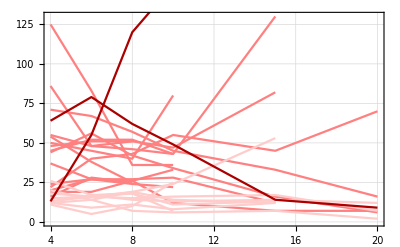

```mathematica
prnaNTL = 
NTdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTM = 
NTdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTH = 
NTdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNT = Show[prnaNTM,prnaNTL, prnaNTH]
```

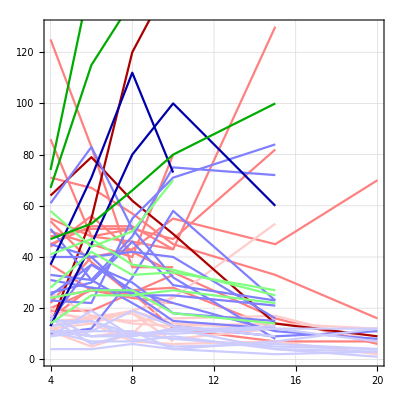

```mathematica
Show[prnaNT,prnaTA,prnaTL,AspectRatio->1]
```

#### %Translation :

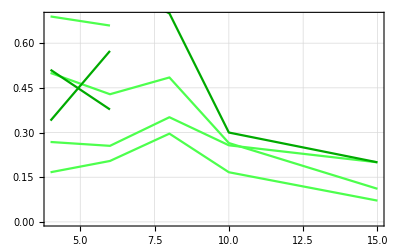

```mathematica
ptransTLL=TLdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLM=TLdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLH=TLdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTL = Show[ptransTLM,ptransTLL, ptransTLH]
```

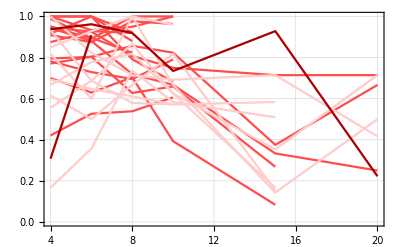

```mathematica
ptransNTL=NTdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTM=NTdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTH=NTdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNT = Show[ptransNTM,ptransNTL, ptransNTH]
```

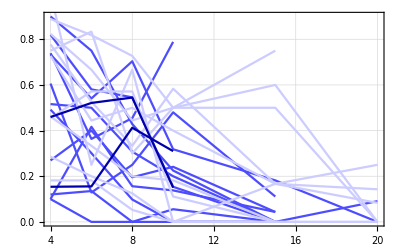

```mathematica
ptransTAL=TAdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAM=TAdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAH=TAdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTA = Show[ptransTAM,ptransTAL, ptransTAH]
```

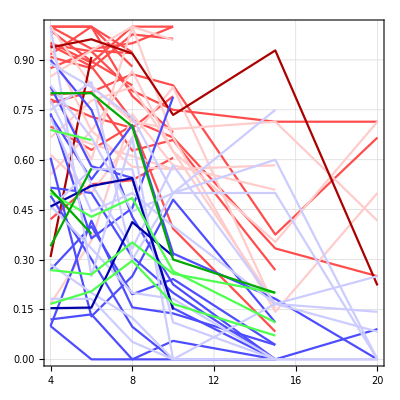

```mathematica
Show[ptransNT,ptransTA,ptransTL,AspectRatio->1]
```

#### # Tethered :

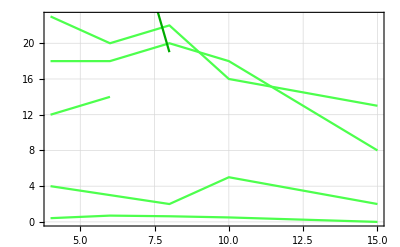

```mathematica
ptethTLL=TLdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLM=TLdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLH=TLdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTL = Show[ptethTLM,ptethTLL, ptethTLH]
```

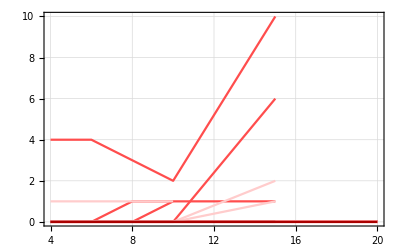

```mathematica
ptethNTL=NTdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTM=NTdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTH=NTdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNT = Show[ptethNTM,ptethNTL, ptethNTH]
```

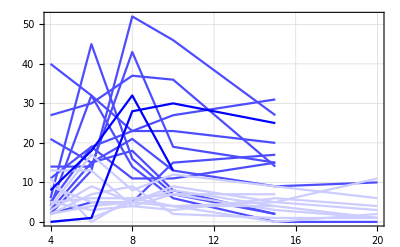

```mathematica
ptethTAL=TAdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAM=TAdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAH=TAdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Blue,Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTA = Show[ptethTAM,ptethTAL, ptethTAH]
```

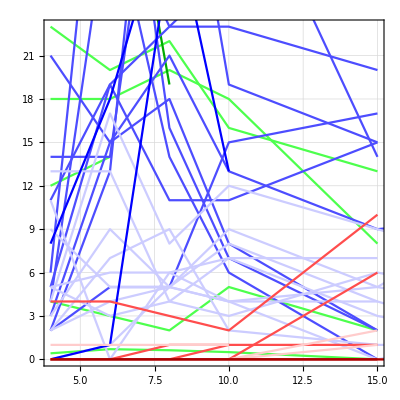

```mathematica
Show[ptethTL,ptethTA,ptethNT,AspectRatio->1]
```

#### % cy3 accumulation :

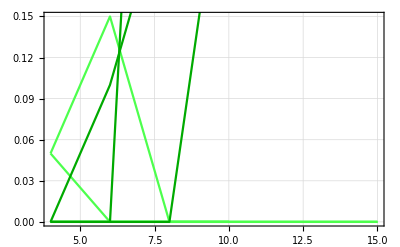

```mathematica
paccumTLL=TLdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=TLdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=TLdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH]
```

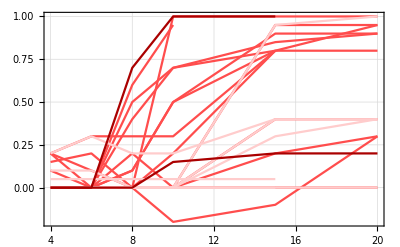

```mathematica
paccumNTL=NTdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=NTdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=NTdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH]
```

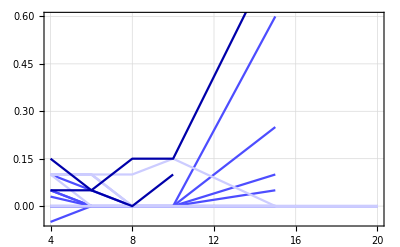

```mathematica
paccumTAL=TAdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=TAdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=TAdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH]
```

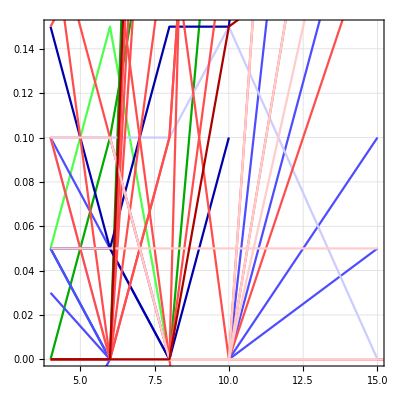

```mathematica
Show[paccumTL,paccumTA,paccumNT,AspectRatio->1]
```

### Totals :

```mathematica
Row[{StringForm["Binned by # RNA per cell at Frame `` : <20,  20-80,  <80   ",o]}]
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
Row[{Show[prnaTAH,prnaNTH,prnaTLH,AspectRatio->1,PlotLabel->"High RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150],
Show[prnaTAM,prnaNTM,prnaTLM,AspectRatio->1,PlotLabel->"Med RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150],
Show[prnaTLL,prnaTAL,prnaNTL,prnaTLL,AspectRatio->1,PlotLabel->"Lo RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150]
}]
Row[{Show[paccumTLH,paccumTAH,paccumNTH,AspectRatio->1,PlotLabel->"High Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLM,paccumTAM,paccumNTM,AspectRatio->1,PlotLabel->"Med Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLL,paccumTAL,paccumNTL,AspectRatio->1,PlotLabel->"Lo Accum",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[ptransTLH,ptransTAH,ptransNTH,AspectRatio->1,PlotLabel->"High Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLM,ptransTAM,ptransNTM,AspectRatio->1,PlotLabel->"Med Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLL,ptransTAL,ptransNTL,AspectRatio->1,PlotLabel->"Lo Trans",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]

(*
Row[{"***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore!   "}]
*)
```

Binned by # RNA per cell at Frame 4 : <20,  20-80,  <80

TA  31   inc 4   lo 10   med 11   hi 2

NT  31   inc 3   lo 9   med 15   hi 2

TL  13   inc 4   lo 0    med 5    hi 3

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

### Graph the %accumulation at 10h for HML w a scatter plot

```mathematica
accumNTL= Table[NTdataL[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataL,1}];
accumNTM= Table[NTdataM[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataM,1}];
accumNTH= Table[NTdataH[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataH,1}];accumTLL= Table[TLdataL[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataL,1}];
accumTLM= Table[TLdataM[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataM,1}];
accumTLH= Table[TLdataH[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataH,1}];
accumTAL= Table[TAdataL[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataL,1}];
accumTAM= Table[TAdataM[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataM,1}];
accumTAH= Table[TAdataH[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataH,1}];
```

```mathematica
accumTLall = Join[accumTLL, accumTLM, accumTLH];
accumTAall = Join[accumTAL, accumTAM, accumTAH];
accumNTall = Join[accumNTL, accumNTM, accumNTH];
```

#### % cy3 accumulation :

```mathematica
paccumTLL=accumTLL//ListPlot[#,PlotStyle->Lighter[Green,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=accumTLM//ListPlot[#,PlotStyle->Lighter[Green,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=accumTLH//ListPlot[#,PlotStyle->Darker[Green],PlotTheme->"Detailed",PlotRange->All]&;
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH,PlotRange-> All]
```

-Graphics-

```mathematica
paccumNTL=accumNTL//ListPlot[#,PlotStyle->Lighter[Red,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=accumNTM//ListPlot[#,PlotStyle->Lighter[Red,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=accumNTH//ListPlot[#,PlotStyle->Darker[Red],PlotTheme->"Detailed",PlotRange->All]&;
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH, PlotRange-> {0,1}]
```

-Graphics-

```mathematica
paccumTAL=accumTAL//ListPlot[#,PlotStyle->Lighter[Blue,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=accumTAM//ListPlot[#,PlotStyle->Lighter[Blue,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=accumTAH//ListPlot[#,PlotStyle->Darker[Blue],PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH,PlotRange-> {0,1}]
```

-Graphics-

```mathematica
accumTLall
```

{{2.04175,0.},{1.98706,0.},{2.08865,0.},{2.08206,0.},{1.98164,0.},{2.04055,0.7},{1.93006,0.9},{2.06982,0.3}}

```mathematica
pBW = BoxWhiskerChart[{accumNTall⟦All,2⟧,accumTLall⟦All,2⟧,accumTAall⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, ALL BINS"];
pBWL = BoxWhiskerChart[{accumNTL⟦All,2⟧,accumTLL⟦All,2⟧,accumTAL⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, Bin LO", PlotRange -> {0,1}];
pBWM = BoxWhiskerChart[{accumNTM⟦All,2⟧,accumTLM⟦All,2⟧,accumTAM⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, Bin MED"];
pBWH = BoxWhiskerChart[{accumNTH⟦All,2⟧,accumTLH⟦All,2⟧,accumTAH⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, Bin HI"];
Row[{pBW, pBWL, pBWM, pBWH
}]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{"NT, TL, and TA accumulation% at 10h
The MEDIAN is represented as a black line. 
The MEAN of each is 0"
}]
Row[{Show[pBW,paccumNT,paccumTL,paccumTA,AspectRatio->1,PlotRange->All  ]
}]
```

NT, TL, and TA accumulation% at 10h
The MEDIAN is represented as a black line. 
The MEAN of each is 0

-Graphics-

## Binning based on Accumulation in cell at frames 1-5

```mathematica
NTdata//Dimensions
TAdata//Dimensions
TLdata//Dimensions
```

{31,7,1}

{31,7,1}

{13,7,1}

```mathematica
NTdata =Join[myNT1,myNT2];
TAdata = Join[myTA1,myTA2];
TLdata = Join[myTL2];
```

```mathematica
(* 
TLdata = myTL2⟦4,Flatten@Position[myTL2⟦4⟧,""]⟧=0
```

```mathematica
rmNTdata = NTdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTLdata = TLdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTAdata = TAdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
```

```mathematica
(* USE THESE INSTEAD if you dont want to remove high accum data... 


NTdata0= NTdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
NTdataL= NTdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
NTdataM= NTdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤1.]&;
NTdataH= NTdata/.""->0.//Cases[#,x_/; 1.≤ Total[x⟦4,1,2;;6,2⟧]]&;
TAdata0= TAdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
TAdataL= TAdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
TAdataM= TAdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤ 1.]&;
TAdataH= TAdata/.""->0.//Cases[#,x_/; 1.≤Total[x⟦4,1,2;;6,2⟧]]&;
TLdata0= TLdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
TLdataL= TLdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]<.25]&;
TLdataM= TLdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤1.]&;
TLdataH= TLdata/.""->0.//Cases[#,x_/; 1.≤Total[x⟦4,1,2;;6,2⟧]]&;
```

```mathematica
p = 1.5
NTdata0= rmNTdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
NTdataL= rmNTdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
NTdataM= rmNTdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤p]&;
NTdataH= rmNTdata/.""->0.//Cases[#,x_/; p≤ Total[x⟦4,1,2;;6,2⟧]]&;
TAdata0= rmTAdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;TAdataL= rmTAdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
TAdataM= rmTAdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤ 1p]&;
TAdataH= rmTAdata/.""->0.//Cases[#,x_/; p≤Total[x⟦4,1,2;;6,2⟧]]&;
TLdata0= rmTLdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;TLdataL= rmTLdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]<.25]&;
TLdataM= rmTLdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤p]&;
TLdataH= rmTLdata/.""->0.//Cases[#,x_/; p≤Total[x⟦4,1,2;;6,2⟧]]&;
```

1.5

```mathematica
Table[Total[TLdata[[j,4,1,2;;6,2]]],{j,1,Length@TLdata,1}]
```

{0.+3 ,0.+3 ,1.9,2.6,0.,0.+3 ,0.+,0.2,0.+,4 +f,0.05,0.7,0.05+4 }

```mathematica
(*
NTdata0=NTdata//Cases[#,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus]&;
NTdataL=Cases[NTdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
NTdataL=Cases[NTdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
NTdataM=Cases[NTdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]≤.75];
NTdataH=Cases[NTdata,x_/; 75≤Total[x[[4,1,2;;6,2]]]];
TAdata0=Cases[TAdata,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus];TAdataL=Cases[TAdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
TAdataM=Cases[TAdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]<.75];
TAdataH=Cases[TAdata,x_/; 75≤Total[x[[4,1,2;;6,2]]]];
TLdata0=TLdata//Cases[3,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus]&;TLdataL=Cases[TLdata,x_/; 0≤Total[x[[4,1,2;;6,2]]]<.25];
TLdataM=Cases[TLdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]≤.75];
TLdataH=Cases[TLdata,x_/; .75≤Total[x[[4,1,2;;6,2]]]];
```

```mathematica
Row[{"TA  ",Length@TAdata ," " ,Length@TAdata0," " ,Length@TAdataL ," " ,Length@TAdataM ," " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ," " ,Length@NTdata0," " ,Length@NTdataL ," " ,Length@NTdataM ," " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ," " ,Length@TLdata0," " ,Length@TLdataL ," " ,Length@TLdataM ," " ,Length@TLdataH}]
```

TA  31 0 24 4 2

NT  31 0 13 5 14

TL  13 0 9 1 2

TA  31 0 24 4 2

NT  31 0 13 7 13

TL  13 0 9 1 2

### Graphs...

#### RNA :

```mathematica
prnaTAL = 
TAdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAM = 
TAdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAH = 
TAdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
```

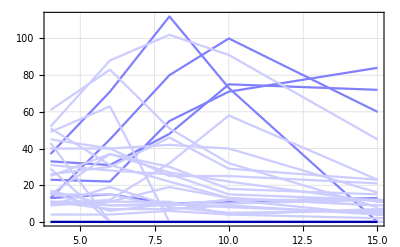

```mathematica
prnaTA = Show[prnaTAM,prnaTAL, prnaTAH]
```

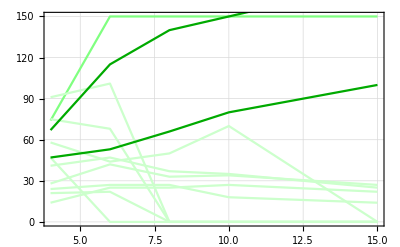

```mathematica
prnaTLL = 
TLdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLM = 
TLdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLH = 
TLdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTL = Show[prnaTLM,prnaTLL, prnaTLH]
```

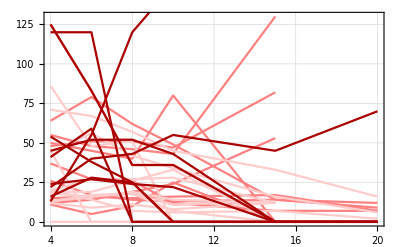

```mathematica
prnaNTL = 
NTdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTM = 
NTdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTH = 
NTdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNT = Show[prnaNTM,prnaNTL, prnaNTH]
```

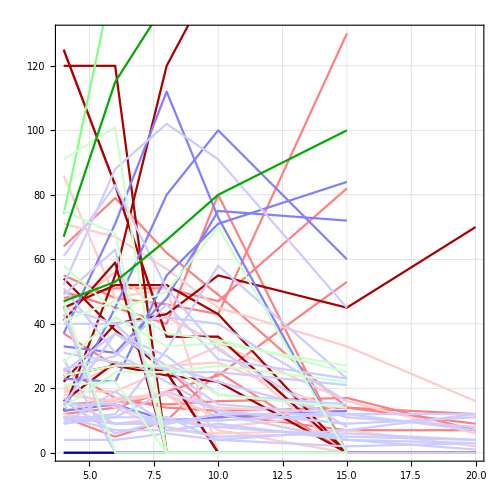

```mathematica
Show[prnaNT,prnaTA,prnaTL,AspectRatio->1]
```

#### %Translation :

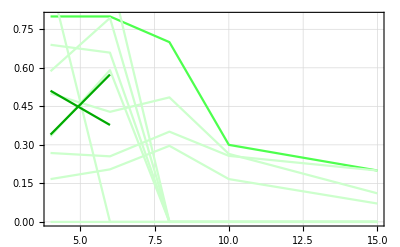

```mathematica
ptransTLL=TLdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLM=TLdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLH=TLdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTL = Show[ptransTLM,ptransTLL, ptransTLH]
```

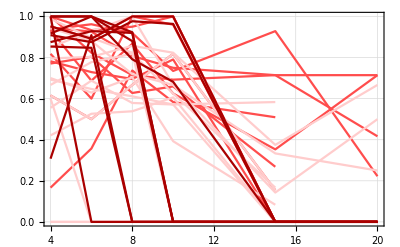

```mathematica
ptransNTL=NTdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTM=NTdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTH=NTdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNT = Show[ptransNTM,ptransNTL, ptransNTH]
```

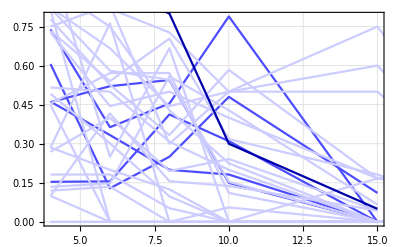

```mathematica
ptransTAL=TAdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAM=TAdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAH=TAdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTA = Show[ptransTAM,ptransTAL, ptransTAH]
```

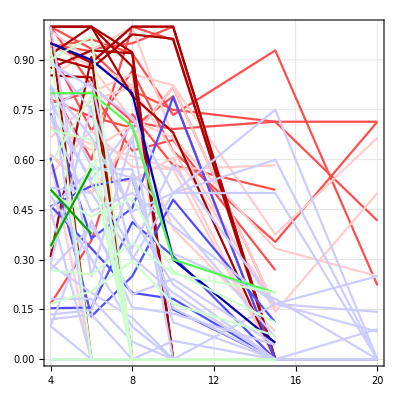

```mathematica
Show[ptransNT,ptransTA,ptransTL,AspectRatio->1]
```

#### # Tethered :

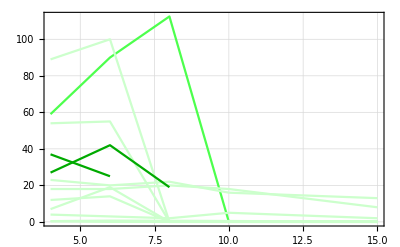

```mathematica
ptethTLL=TLdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLM=TLdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLH=TLdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTL = Show[ptethTLM,ptethTLL, ptethTLH]
```

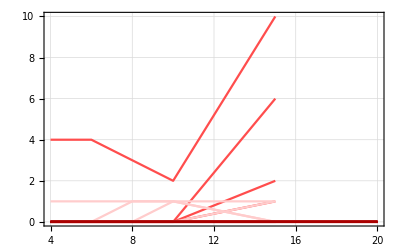

```mathematica
ptethNTL=NTdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTM=NTdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTH=NTdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNT = Show[ptethNTM,ptethNTL, ptethNTH]
```

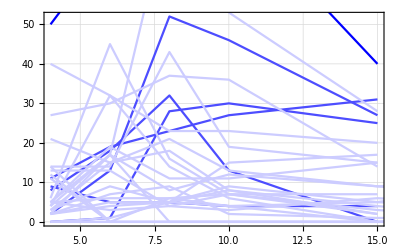

```mathematica
ptethTAL=TAdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAM=TAdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAH=TAdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Blue,Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTA = Show[ptethTAM,ptethTAL, ptethTAH]
```

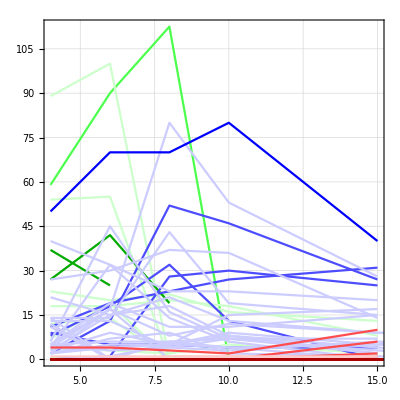

```mathematica
Show[ptethTL,ptethTA,ptethNT,AspectRatio->1]
```

#### % cy3 accumulation :

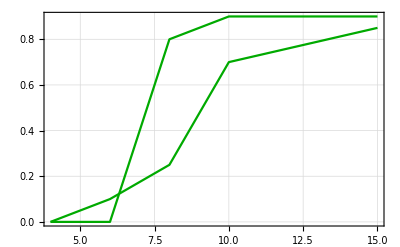

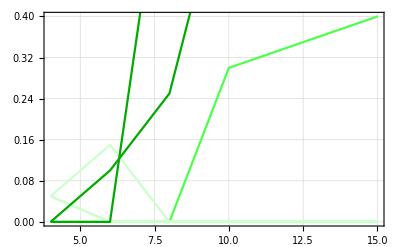

```mathematica
paccumTLL=TLdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=TLdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=TLdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH]
```

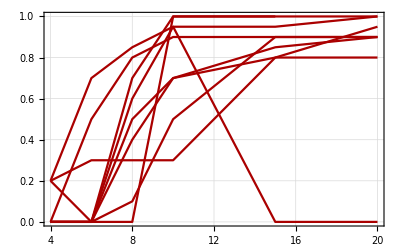

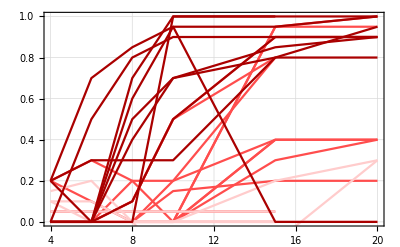

```mathematica
paccumNTL=NTdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=NTdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=NTdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH]
```

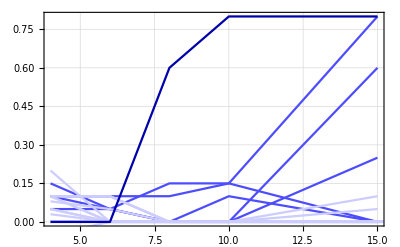

```mathematica
paccumTAL=TAdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=TAdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=TAdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH]
```

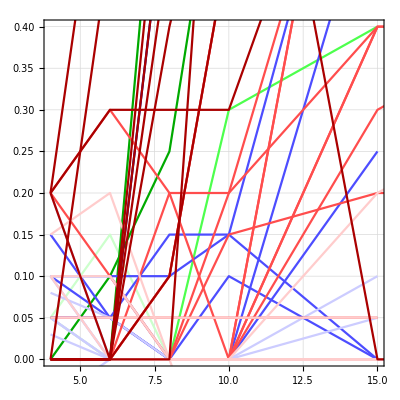

```mathematica
Show[paccumTL,paccumTA,paccumNT,AspectRatio->1]
```

#### Totals :

Binned by % accumulation: <25%,  25-75%,  >75%

TA  31   inc 0   lo 24   med 5   hi 1

NT  31   inc 0   lo 13   med 11   hi 9

TL  13   inc 0   lo 9    med 1    hi 2

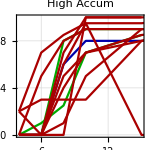
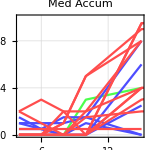
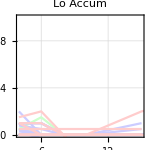

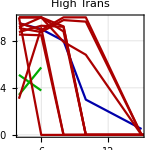
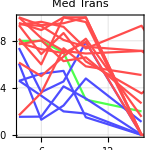
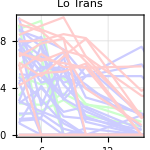

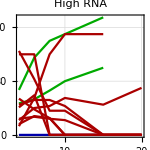
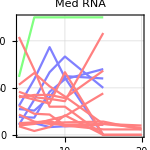

***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore! 
***NOT biologically relevant, not actually happening!

```mathematica
Row[{"Binned by % accumulation: <25%,  25-75%,  >75%"}]
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
Row[{Show[paccumTLH,paccumTAH,paccumNTH,AspectRatio->1,PlotLabel->"High Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLM,paccumTAM,paccumNTM,AspectRatio->1,PlotLabel->"Med Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLL,paccumTAL,paccumNTL,AspectRatio->1,PlotLabel->"Lo Accum",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[ptransTLH,ptransTAH,ptransNTH,AspectRatio->1,PlotLabel->"High Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLM,ptransTAM,ptransNTM,AspectRatio->1,PlotLabel->"Med Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLL,ptransTAL,ptransNTL,AspectRatio->1,PlotLabel->"Lo Trans",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[prnaTLH,prnaTAH,prnaNTH,AspectRatio->1,PlotLabel->"High RNA",PlotRange->{{4,15},{0,All}},ImageSize->150],
Show[prnaTLM,prnaTAM,prnaNTM,AspectRatio->1,PlotLabel->"Med RNA",PlotRange->{{4,15},{0,All}},ImageSize->150],
Show[prnaTLL,prnaTAL,prnaNTL,AspectRatio->1,PlotLabel->"Lo RNA",PlotRange->{{4,15},{0,All}},ImageSize->150]
}]
Row[{"***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore! 
***NOT biologically relevant, not actually happening!"}]
```

NOTE!!! This is neglecting that since I’m doing the total I’m not actually 
doing 50-75% or over 75% or whatever, I’m totalling multiple points!!!

## Binning based on Accumulation in cell at frames 1-5 WITH BoxWhisk charts

```mathematica
NTdata//Dimensions
TAdata//Dimensions
TLdata//Dimensions
```

{31,7,1}

{31,7,1}

{13,7,1}

```mathematica
NTdata =Join[myNT1,myNT2];
TAdata = Join[myTA1,myTA2];
TLdata = Join[myTL2];
```

```mathematica
(* 
TLdata = myTL2⟦4,Flatten@Position[myTL2⟦4⟧,""]⟧=0
```

```mathematica
rmNTdata = NTdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTLdata = TLdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTAdata = TAdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
```

```mathematica
(* USE THESE INSTEAD if you dont want to remove high accum data... 


NTdata0= NTdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
NTdataL= NTdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
NTdataM= NTdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤1.]&;
NTdataH= NTdata/.""->0.//Cases[#,x_/; 1.≤ Total[x⟦4,1,2;;6,2⟧]]&;
TAdata0= TAdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
TAdataL= TAdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
TAdataM= TAdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤ 1.]&;
TAdataH= TAdata/.""->0.//Cases[#,x_/; 1.≤Total[x⟦4,1,2;;6,2⟧]]&;
TLdata0= TLdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
TLdataL= TLdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]<.25]&;
TLdataM= TLdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤1.]&;
TLdataH= TLdata/.""->0.//Cases[#,x_/; 1.≤Total[x⟦4,1,2;;6,2⟧]]&;
```

```mathematica
p = 1.5
NTdata0= rmNTdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
NTdataL= rmNTdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
NTdataM= rmNTdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤p]&;
NTdataH= rmNTdata/.""->0.//Cases[#,x_/; p≤ Total[x⟦4,1,2;;6,2⟧]]&;
TAdata0= rmTAdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;TAdataL= rmTAdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
TAdataM= rmTAdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤ 1p]&;
TAdataH= rmTAdata/.""->0.//Cases[#,x_/; p≤Total[x⟦4,1,2;;6,2⟧]]&;
TLdata0= rmTLdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;TLdataL= rmTLdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]<.25]&;
TLdataM= rmTLdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤p]&;
TLdataH= rmTLdata/.""->0.//Cases[#,x_/; p≤Total[x⟦4,1,2;;6,2⟧]]&;
```

1.5

```mathematica
Table[Total[TLdata[[j,4,1,2;;6,2]]],{j,1,Length@TLdata,1}]
```

{0.+3 ,0.+3 ,1.9,2.6,0.,0.+3 ,0.+,0.2,0.+,4 +f,0.05,0.7,0.05+4 }

```mathematica
(*
NTdata0=NTdata//Cases[#,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus]&;
NTdataL=Cases[NTdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
NTdataL=Cases[NTdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
NTdataM=Cases[NTdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]≤.75];
NTdataH=Cases[NTdata,x_/; 75≤Total[x[[4,1,2;;6,2]]]];
TAdata0=Cases[TAdata,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus];TAdataL=Cases[TAdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
TAdataM=Cases[TAdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]<.75];
TAdataH=Cases[TAdata,x_/; 75≤Total[x[[4,1,2;;6,2]]]];
TLdata0=TLdata//Cases[3,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus]&;TLdataL=Cases[TLdata,x_/; 0≤Total[x[[4,1,2;;6,2]]]<.25];
TLdataM=Cases[TLdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]≤.75];
TLdataH=Cases[TLdata,x_/; .75≤Total[x[[4,1,2;;6,2]]]];
```

```mathematica
Row[{"TA  ",Length@TAdata ," " ,Length@TAdata0," " ,Length@TAdataL ," " ,Length@TAdataM ," " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ," " ,Length@NTdata0," " ,Length@NTdataL ," " ,Length@NTdataM ," " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ," " ,Length@TLdata0," " ,Length@TLdataL ," " ,Length@TLdataM ," " ,Length@TLdataH}]
```

TA  31 0 24 4 2

NT  31 0 13 5 14

TL  13 0 9 1 2

TA  31 0 24 4 2

NT  31 0 13 7 13

TL  13 0 9 1 2

### Graphs...

#### RNA :

```mathematica
prnaTAL = 
TAdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAM = 
TAdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAH = 
TAdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
```

```mathematica
prnaTA = Show[prnaTAM,prnaTAL, prnaTAH]
```

-Graphics-

```mathematica
prnaTLL = 
TLdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLM = 
TLdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLH = 
TLdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTL = Show[prnaTLM,prnaTLL, prnaTLH]
```

-Graphics-

```mathematica
prnaNTL = 
NTdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTM = 
NTdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTH = 
NTdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNT = Show[prnaNTM,prnaNTL, prnaNTH]
```

-Graphics-

```mathematica
Show[prnaNT,prnaTA,prnaTL,AspectRatio->1]
```

-Graphics-

#### %Translation :

```mathematica
ptransTLL=TLdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLM=TLdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLH=TLdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTL = Show[ptransTLM,ptransTLL, ptransTLH]
```

-Graphics-

```mathematica
ptransNTL=NTdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTM=NTdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTH=NTdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNT = Show[ptransNTM,ptransNTL, ptransNTH]
```

-Graphics-

```mathematica
ptransTAL=TAdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAM=TAdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAH=TAdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTA = Show[ptransTAM,ptransTAL, ptransTAH]
```

-Graphics-

```mathematica
Show[ptransNT,ptransTA,ptransTL,AspectRatio->1]
```

-Graphics-

#### # Tethered :

```mathematica
ptethTLL=TLdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLM=TLdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLH=TLdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTL = Show[ptethTLM,ptethTLL, ptethTLH]
```

-Graphics-

```mathematica
ptethNTL=NTdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTM=NTdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTH=NTdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNT = Show[ptethNTM,ptethNTL, ptethNTH]
```

-Graphics-

```mathematica
ptethTAL=TAdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAM=TAdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAH=TAdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Blue,Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTA = Show[ptethTAM,ptethTAL, ptethTAH]
```

-Graphics-

```mathematica
Show[ptethTL,ptethTA,ptethNT,AspectRatio->1]
```

-Graphics-

#### % cy3 accumulation :

```mathematica
paccumTLL=TLdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=TLdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=TLdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH]
```

-Graphics-

-Graphics-

```mathematica
paccumNTL=NTdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=NTdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=NTdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH]
```

-Graphics-

-Graphics-

```mathematica
paccumTAL=TAdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=TAdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=TAdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH]
```

-Graphics-

```mathematica
Show[paccumTL,paccumTA,paccumNT,AspectRatio->1]
```

-Graphics-

#### Totals :

```mathematica
Row[{"Binned by % accumulation: <25%,  25-75%,  >75%"}]
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
Row[{Show[paccumTLH,paccumTAH,paccumNTH,AspectRatio->1,PlotLabel->"High Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLM,paccumTAM,paccumNTM,AspectRatio->1,PlotLabel->"Med Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLL,paccumTAL,paccumNTL,AspectRatio->1,PlotLabel->"Lo Accum",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[ptransTLH,ptransTAH,ptransNTH,AspectRatio->1,PlotLabel->"High Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLM,ptransTAM,ptransNTM,AspectRatio->1,PlotLabel->"Med Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLL,ptransTAL,ptransNTL,AspectRatio->1,PlotLabel->"Lo Trans",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[prnaTLH,prnaTAH,prnaNTH,AspectRatio->1,PlotLabel->"High RNA",PlotRange->{{4,15},{0,All}},ImageSize->150],
Show[prnaTLM,prnaTAM,prnaNTM,AspectRatio->1,PlotLabel->"Med RNA",PlotRange->{{4,15},{0,All}},ImageSize->150],
Show[prnaTLL,prnaTAL,prnaNTL,AspectRatio->1,PlotLabel->"Lo RNA",PlotRange->{{4,15},{0,All}},ImageSize->150]
}]
Row[{"***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore! 
***NOT biologically relevant, not actually happening!"}]
```

Binned by % accumulation: <25%,  25-75%,  >75%

TA  31   inc 0   lo 24   med 5   hi 1

NT  31   inc 0   lo 13   med 11   hi 9

TL  13   inc 0   lo 9    med 1    hi 2

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore! 
***NOT biologically relevant, not actually happening!

NOTE!!! This is neglecting that since I’m doing the total I’m not actually 
doing 50-75% or over 75% or whatever, I’m totalling multiple points!!!

### Determine point of accumulation getting above 50% ***use this to show TIME when cell accumulated product ****ALL DEV!!!!!****

```mathematica
paccumTLL=TLdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=TLdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=TLdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH]
```

```mathematica
Cases[TLdata,x_/; Head[x⟦p,1,o,2⟧]== String]
```

Part::partd: Part specification {{TL05},{{{hours,#RNA},{4.,91.},{6.,101.},{8.,},{10.,},{15.,}}},{{{hours,%Translating},{4.,0.901099},{6.,0.970297},{8.,},{10.,},{15.,}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,},{10.,},{15.,}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,dead},{10.,dead},{15.,dead}}},{{{hours,AGO},{4.,2.},{6.,2.5},{8.,},{10.,},{15.,}}},{{{hours,Tethering?},{4.,89.},{6.,100.},{8.,},{10.,},{15.,}}}}⟦0,1,4,2⟧ is longer than depth of object.

Part::partd: Part specification {{TL04},{{{hours,#RNA},{4.,21.},{6.,22.},{8.,},{10.,},{15.,}}},{{{hours,%Translating},{4.,0.333333},{6.,0.590909},{8.,},{10.,},{15.,}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,},{10.,},{15.,}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,dead},{10.,dead},{15.,dead}}},{{{hours,AGO},{4.,0.},{6.,1.},{8.,},{10.,},{15.,}}},{{{hours,Tethering?},{4.,7.},{6.,19.},{8.,},{10.,},{15.,}}}}⟦0,1,4,2⟧ is longer than depth of object.

Part::partd: Part specification {{TL12},{{{hours,#RNA},{4.,67.},{6.,115.},{8.,140.},{10.,150.},{15.,175.}}},{{{hours,%Translating},{4.,0.34},{6.,0.573913},{8.,na},{10.,na},{15.,na}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.1},{8.,0.25},{10.,0.7},{15.,0.85}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,f},{10.,t},{15.,t}}},{{{hours,AGO},{4.,1.},{6.,2.},{8.,3.},{10.,3.},{15.,3.}}},{{{hours,Tethering?},{4.,37.},{6.,25.},{8.,na},{10.,na},{15.,na}}}}⟦0,1,4,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
Cases[TLdataH[[4,1,1;;All,2]],x_/;x≥.5]
```

Part::partw: Part 4 of … does not exist.

{4,1,2}

```mathematica
TLdataH[[All,4,1,1;;All,2]]
```

{{Cy3 Accum (%),0.,0.1,0.25,0.7,0.85},{Cy3 Accum (%),0.,0.,0.8,0.9,0.9}}

```mathematica
p = 4;
TLdataH//Cases[#,x_/;  x⟦p,1,2;;All,2⟧≥ .5]&
```

{}

```mathematica
Number
```

```mathematica
Table[NTdataH[[All,4,1,2;;All]],{i,1,1,1}]
```

{{{{4.,0.},{6.,0.},{8.,0.},{10.,1.},{15.,1.},{20.,1.}},{{4.,0.2},{6.,0.3},{8.,0.3},{10.,0.3},{15.,0.8},{20.,0.95}},{{4.,0.2},{6.,0.},{8.,0.6},{10.,0.95},{15.,0.},{20.,0.}},{{4.,0.2},{6.,0.7},{8.,0.85},{10.,0.95},{15.,0.95},{20.,1.}},{{4.,0.},{6.,0.5},{8.,0.8},{10.,0.9},{15.,0.9},{20.,0.9}},{{4.,0.},{6.,0.},{8.,0.1},{10.,0.5},{15.,0.9},{20.,0.9}},{{4.,0.},{6.,0.},{8.,0.5},{10.,0.7},{15.,0.8},{20.,0.8}},{{4.,0.},{6.,0.},{8.,0.4},{10.,0.7},{15.,0.85},{20.,0.9}},{{4.,0.},{6.,0.},{8.,0.7},{10.,1.},{15.,1.}}}}

```mathematica
NTdataH[[All,4,1,2;;6]]//TableForm
```

4.
0. | 6.
0. | 8.
0. | 10.
1. | 15.
1.
4.
0.2 | 6.
0.3 | 8.
0.3 | 10.
0.3 | 15.
0.8
4.
0.2 | 6.
0. | 8.
0.6 | 10.
0.95 | 15.
0.
4.
0.2 | 6.
0.7 | 8.
0.85 | 10.
0.95 | 15.
0.95
4.
0. | 6.
0.5 | 8.
0.8 | 10.
0.9 | 15.
0.9
4.
0. | 6.
0. | 8.
0.1 | 10.
0.5 | 15.
0.9
4.
0. | 6.
0. | 8.
0.5 | 10.
0.7 | 15.
0.8
4.
0. | 6.
0. | 8.
0.4 | 10.
0.7 | 15.
0.85
4.
0. | 6.
0. | 8.
0.7 | 10.
1. | 15.
1.

```mathematica
NTdataH[[All,4,1,2;;6]]//Cases[#,x_/; x⟦1,2⟧>0]&//TableForm
```

4.
0.2 | 6.
0.3 | 8.
0.3 | 10.
0.3 | 15.
0.8
4.
0.2 | 6.
0. | 8.
0.6 | 10.
0.95 | 15.
0.
4.
0.2 | 6.
0.7 | 8.
0.85 | 10.
0.95 | 15.
0.95

```mathematica
Table[NTdataH⟦4,1,i,2⟧>0,{i,2,6,1}]
```

{False,False,False,True,True}

```mathematica
NTdataH[[All,4]]
```

{{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,1.},{15.,1.},{20.,1.}}},{{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.3},{8.,0.3},{10.,0.3},{15.,0.8},{20.,0.95}}},{{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.},{8.,0.6},{10.,0.95},{15.,0.},{20.,0.}}},{{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.7},{8.,0.85},{10.,0.95},{15.,0.95},{20.,1.}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.5},{8.,0.8},{10.,0.9},{15.,0.9},{20.,0.9}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.1},{10.,0.5},{15.,0.9},{20.,0.9}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.5},{10.,0.7},{15.,0.8},{20.,0.8}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.4},{10.,0.7},{15.,0.85},{20.,0.9}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.7},{10.,1.},{15.,1.}}}}

0.5

```mathematica
rmTLdata[[All,4,1,2;;All]]
```

{{{4.,0.},{6.,0.},{8.,},{10.,},{15.,}},{{4.,0.},{6.,0.},{8.,},{10.,},{15.,}},{{4.,0.},{6.,0.1},{8.,0.25},{10.,0.7},{15.,0.85}},{{4.,0.},{6.,0.},{8.,0.8},{10.,0.9},{15.,0.9}},{{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}},{{4.,0.},{6.,0.},{8.,},{10.,},{15.,}},{{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,}},{{4.,0.05},{6.,0.15},{8.,0.},{10.,0.},{15.,0.}},{{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,}},{{4.,0.05},{6.,0.},{8.,0.},{10.,0.},{15.,0.}},{{4.,0.},{6.,0.},{8.,0.},{10.,0.3},{15.,0.4}},{{4.,0.05},{6.,},{8.,},{10.,},{15.,}}}

```mathematica
Dimensions/@rmTLdata
```

{{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1}}

```mathematica
p = 0;
Cases[rmTLdata,x_/; AnyTrue[p≤  Table[x⟦4,1,i,2⟧,{i,2,6,1}]]]
```

```mathematica
Cases[rmTLdata,x_/; AnyTrue[p≤  x⟦4,1,2;;All,2⟧]]
```

{}

```mathematica
AnyTrue[p≤  rmTLdata⟦All,4,1,2;;All,2⟧]
```

AnyTrue[0≤{{0.,0.,,,},{0.,0.,,,},{0.,0.1,0.25,0.7,0.85},{0.,0.,0.8,0.9,0.9},{0.,0.,0.,0.,0.},{0.,0.,,,},{0.,0.,0.,0.,},{0.05,0.15,0.,0.,0.},{0.,0.,0.,0.,},{0.05,0.,0.,0.,0.},{0.,0.,0.,0.3,0.4},{0.05,,,,}}]

```mathematica
temp =  rmTLdata⟦All,4,1,2;;All,2⟧
```

{{0.,0.,,,},{0.,0.,,,},{0.,0.1,0.25,0.7,0.85},{0.,0.,0.8,0.9,0.9},{0.,0.,0.,0.,0.},{0.,0.,,,},{0.,0.,0.,0.,},{0.05,0.15,0.,0.,0.},{0.,0.,0.,0.,},{0.05,0.,0.,0.,0.},{0.,0.,0.,0.3,0.4},{0.05,,,,}}

### Graph the %accumulation at 10h for HML w a scatter plot

```mathematica
accumNTL= Table[NTdataL[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataL,1}];
accumNTM= Table[NTdataM[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataM,1}];
accumNTH= Table[NTdataH[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataH,1}];accumTLL= Table[TLdataL[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataL,1}];
accumTLM= Table[TLdataM[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataM,1}];
accumTLH= Table[TLdataH[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataH,1}];
accumTAL= Table[TAdataL[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataL,1}];
accumTAM= Table[TAdataM[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataM,1}];
accumTAH= Table[TAdataH[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataH,1}];
```

```mathematica
accumTLall = Join[accumTLL, accumTLM, accumTLH];
accumTAall = Join[accumTAL, accumTAM, accumTAH];
accumNTall = Join[accumNTL, accumNTM, accumNTH];
```

#### % cy3 accumulation :

```mathematica
paccumTLL=accumTLL//ListPlot[#,PlotStyle->Lighter[Green,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=accumTLM//ListPlot[#,PlotStyle->Lighter[Green,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=accumTLH//ListPlot[#,PlotStyle->Darker[Green],PlotTheme->"Detailed",PlotRange->All]&;
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH,PlotRange-> All]
```

-Graphics-

```mathematica
paccumNTL=accumNTL//ListPlot[#,PlotStyle->Lighter[Red,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=accumNTM//ListPlot[#,PlotStyle->Lighter[Red,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=accumNTH//ListPlot[#,PlotStyle->Darker[Red],PlotTheme->"Detailed",PlotRange->All]&;
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH, PlotRange-> {0,1}]
```

-Graphics-

```mathematica
paccumTAL=accumTAL//ListPlot[#,PlotStyle->Lighter[Blue,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=accumTAM//ListPlot[#,PlotStyle->Lighter[Blue,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=accumTAH//ListPlot[#,PlotStyle->Darker[Blue],PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH,PlotRange-> {0,1}]
```

-Graphics-

```mathematica
pBW = BoxWhiskerChart[{accumNTall⟦All,2⟧,accumTLall⟦All,2⟧,accumTAall⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], Axes]
```

-Graphics-

```mathematica
Row[{"NT, TL, and TA accumulation% at 10h
The MEDIAN is represented as a black line. 
The MEAN of each is 0"
}]
Row[{Show[pBW,paccumNT,paccumTL,paccumTA,AspectRatio->1,PlotRange->All]
}]
```

NT, TL, and TA accumulation% at 10h
The MEDIAN is represented as a black line. 
The MEAN of each is 0

-Graphics-

### Calculating the averages of replicate data set means....

```mathematica
Table[Mean[{AvgtethNT2[[i]],AvgtethNT1[[i]]}],{i,1,Length@AvgtethNT2,1}]
```

{}

```mathematica
Table[{AvgtethNT2[[i]],AvgtethNT1[[i]]},{i,1,Length@AvgtethNT2,1}]
```

{}

```mathematica
Mean/@Table[AvgtethNT2[i],{i,1,Length@AvgtethNT2,1}]
```

{}

```mathematica
totalAvgtethNT=Table[Mean[{AvgtethNT2[[i]],AvgtethNT1[[i]]}],{i,1,Length@AvgtethNT2,1}]
totalAvgtethNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

{}

-Graphics-

# OLD reading in excel stuff

### #RNA

#### UPDATED to show the 10 - 20 - 23 info! NT TL TA

```mathematica
pNT=NTRNA//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgNT=Cases[Table[Mean[Cases[NTRNA[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
mysheet=7;
```

```mathematica
times=myExcel[[mysheet,7;;13,3]]
```

{hours,4.,6.,8.,10.,16.,}

```mathematica
myCells=Flatten[Position[myExcel[[mysheet,7]],x_/;x=="#RNA"]]
```

{5,13,20,27,34,41,48,55,62,69,76,83,90,97,104,111,118,125}

```mathematica
aRNAs=Table[myExcel[[mysheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{#RNA,91.,101.,,,,***accum at f10},{#RNA,21.,22.,,,,},{#RNA,67.,115.,140.,150.,175.,},{#RNA,47.,53.,66.,80.,100.,*Really pretty video but chunky ER or golgi},{#RNA,14.,25.,,,,},{#RNA,75.,68.,,,,},{#RNA,58.,44.,50.,70.,70.,},{#RNA,41.,47.,37.,35.,27.,},{#RNA,34.,,,,,},{#RNA,28.,42.,33.,34.,18.,},{#RNA,53.,65.,46.,36.,29.,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,}}

```mathematica
myTLRNAvT=Transpose[{times,#}]&/@RNAs
```

{{{hours,#RNA},{4.,91.},{6.,101.},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,21.},{6.,22.},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,67.},{6.,115.},{8.,140.},{10.,150.},{16.,150.},{,175.}},{{hours,#RNA},{4.,47.},{6.,53.},{8.,66.},{10.,80.},{16.,100.},{,100.}},{{hours,#RNA},{4.,14.},{6.,25.},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,75.},{6.,68.},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,58.},{6.,44.},{8.,50.},{10.,70.},{16.,80.},{,70.}},{{hours,#RNA},{4.,41.},{6.,47.},{8.,37.},{10.,35.},{16.,28.},{,27.}},{{hours,#RNA},{4.,34.},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,28.},{6.,42.},{8.,33.},{10.,34.},{16.,25.},{,18.}},{{hours,#RNA},{4.,53.},{6.,65.},{8.,46.},{10.,36.},{16.,45.},{,29.}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}}}

```mathematica
rnaTA1
```

{{{4.,16.},{6.,6.},{8.,10.},{10.,8.},{15.,5.},{20.,4.}},{{4.,17.},{6.,9.},{8.,9.},{10.,12.},{15.,4.},{20.,3.}},{{4.,11.},{6.,9.},{8.,10.},{10.,10.},{15.,12.},{20.,12.}},{{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{4.,43.},{6.,},{8.,},{10.,},{15.,},{20.,}},{{4.,4.},{6.,4.},{8.,6.},{10.,4.},{15.,7.},{20.,12.}},{{4.,51.},{6.,31.},{8.,22.},{10.,13.},{15.,9.},{20.,11.}},{{4.,15.},{6.,37.},{8.,27.},{10.,22.},{15.,11.},{20.,8.}},{{4.,15.},{6.,15.},{8.,8.},{10.,5.},{15.,6.},{20.,4.}},{{4.,9.},{6.,11.},{8.,11.},{10.,4.},{15.,2.},{20.,3.}},{{4.,9.},{6.,19.},{8.,9.},{10.,12.},{15.,12.},{20.,7.}},{{4.,11.},{6.,7.},{8.,7.},{10.,9.},{15.,4.},{20.,1.}},{{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}}}

```mathematica
tethTA1//ListPlot[#]
```

ListPlot::lpn: #1 is not a list of numbers or pairs of numbers.

ListPlot[#1][{{{{hours,Tethering?},{4.,3.},{6.,9.},{8.,5.},{10.,9.},{15.,5.},{20.,3.}}},{{{hours,Tethering?},{4.,5.},{6.,6.},{8.,6.},{10.,7.},{15.,3.},{20.,1.}}},{{{hours,Tethering?},{4.,11.},{6.,0.},{8.,6.},{10.,4.},{15.,0.},{20.,2.}}},{{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}}},{{{hours,Tethering?},{4.,12.},{6.,},{8.,},{10.,},{15.,},{20.,}}},{{{hours,Tethering?},{4.,0.},{6.,1.},{8.,5.},{10.,4.},{15.,5.},{20.,11.}}},{{{hours,Tethering?},{4.,21.},{6.,15.},{8.,21.},{10.,13.},{15.,9.},{20.,10.}}},{{{hours,Tethering?},{4.,4.},{6.,32.},{8.,14.},{10.,6.},{15.,0.},{20.,0.}}},{{{hours,Tethering?},{4.,13.},{6.,13.},{8.,4.},{10.,3.},{15.,6.},{20.,4.}}},{{{hours,Tethering?},{4.,2.},{6.,7.},{8.,9.},{10.,2.},{15.,1.},{20.,1.}}},{{{hours,Tethering?},{4.,4.},{6.,17.},{8.,8.},{10.,12.},{15.,9.},{20.,6.}}},{{{hours,Tethering?},{4.,2.},{6.,4.},{8.,5.},{10.,8.},{15.,4.},{20.,1.}}},{{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}}}}]

```mathematica
myTLRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgTL=Cases[Table[Mean[Cases[myTLRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Green,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
mysheet=9;
```

```mathematica
times=myExcel[[mysheet,7;;13,3]]
```

{hours,4.,6.,8.,10.,16.,}

```mathematica
myCells=Flatten[Position[myExcel[[mysheet,7]],x_/;x=="#RNA"]]
```

{5,13,20,27,34,41,48,55,62,69,76,83,90,97,104,111,118,125}

```mathematica
RNAs=Table[myExcel[[mysheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{#RNA,10.,12.,32.,58.,32.,},{#RNA,45.,40.,25.,25.,21.,},{#RNA,40.,40.,42.,40.,16.,},{#RNA,26.,30.,46.,29.,23.,},{#RNA,31.,28.,26.,15.,7.,},{#RNA,4.,12.,38.,65.,30.,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,}}

```mathematica
myTARNAvT=Transpose[{times,#}]&/@RNAs
```

{{{hours,#RNA},{4.,10.},{6.,12.},{8.,32.},{10.,58.},{16.,32.},{,}},{{hours,#RNA},{4.,45.},{6.,40.},{8.,25.},{10.,25.},{16.,21.},{,}},{{hours,#RNA},{4.,40.},{6.,40.},{8.,42.},{10.,40.},{16.,16.},{,}},{{hours,#RNA},{4.,26.},{6.,30.},{8.,46.},{10.,29.},{16.,23.},{,}},{{hours,#RNA},{4.,31.},{6.,28.},{8.,26.},{10.,15.},{16.,7.},{,}},{{hours,#RNA},{4.,4.},{6.,12.},{8.,38.},{10.,65.},{16.,30.},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{16.,},{,}}}

```mathematica
pTA=myTARNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgTA=Cases[Table[Mean[Cases[myTARNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Blue,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
Show[pAvgTL,pAvgNT,pAvgTA,PlotRange->All]
```

-Graphics-

```mathematica
Show[pTL,pNT,pTA, pAvgNT,pAvgTL, pAvgTA, PlotRange->{{04,16},{0,160}},FrameLabel->{"time (hr)","# RNA"},BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->400]
```

-Graphics-

### %translating RNA

#### updated to show the 10 - 20 - 23 info! NT, TL, TA

```mathematica
myCells=Flatten[Position[myExcel[[6,7]],x_/;x=="%Translating"]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90}

```mathematica
RNAs=Table[myExcel[[6,7;;14,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myRNAvT=Transpose[{times,#}]&/@RNAs;
```

```mathematica
ptransNT=myRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgtransNT=Cases[Table[Mean[Cases[myRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
mysheet=7;
```

```mathematica
times=myExcel[[mysheet,7;;All,3]]
```

{hours,2.5,4.,6.,8.,10.,13.,16.,}

```mathematica
myCells=Flatten[Position[myExcel[[mysheet,7]],x_/;x=="%Translating"]]
```

{6,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126}

```mathematica
RNAs=Table[myExcel[[mysheet,7;;All,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myTLRNAvT=Transpose[{times,#}]&/@RNAs;
```

```mathematica
ptransTL=myTLRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgtransTL=Cases[Table[Mean[Cases[myTLRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Green,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
mysheet=9;
```

```mathematica
times=myExcel[[mysheet,7;;14,3]]
```

{hours,2.5,4.,6.,8.,10.,13.,16.}

```mathematica
myCells=Flatten[Position[myExcel[[mysheet,7]],x_/;x=="%Translating"]]
```

{6,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126}

```mathematica
RNAs=Table[myExcel[[mysheet,7;;14,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
mytransTARNAvT=Transpose[{times,#}]&/@RNAs;
```

```mathematica
ptransTA=mytransTARNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
ptransAvgTA=Cases[Table[Mean[Cases[mytransTARNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Blue,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
Show[ptransAvgTA,pAvgtransNT,pAvgtransTL, PlotRange->All]
```

-Graphics-

```mathematica
Show[ptransNT,ptransTA,ptransTL, pAvgtransNT,ptransAvgTA,pAvgtransTL,PlotRange->{{04,16},Automatic},FrameLabel->{"time (hr)","# RNA"},BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->400]
```

-Graphics-

### Cy3Accumuln

```mathematica
myCells=Flatten[Position[myExcel[[6,7]],x_/;x=="Cy3 Accum (%)"]]
```

{7,14,21,28,35,42,49,56,63,70,77,84,91}

```mathematica
RNAs=Table[myExcel[[6,7;;14,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myRNAvT=Transpose[{times,#}]&/@RNAs;
```

```mathematica
paccumNT=myRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,0,8,.5}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgaccumNT=Cases[Table[Mean[Cases[myRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
mysheet=7;
```

```mathematica
times=myExcel[[mysheet,7;;14,3]]
```

{hours,2.5,4.,6.,8.,10.,13.,16.}

```mathematica
myCells=Flatten[Position[myExcel[[mysheet,7]],x_/;x=="Cy3 Accum (%)"]]
```

{7,15,22,29,36,43,50,57,64,71,78,85,92,99,106,113,120,127}

```mathematica
RNAs=Table[myExcel[[mysheet,7;;14,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{Cy3 Accum (%),0.,0.,0.,,,,},{Cy3 Accum (%),0.,0.,0.,,,,},{Cy3 Accum (%),0.,0.,0.1,0.25,0.7,0.8,0.85},{Cy3 Accum (%),0.,0.,0.,0.8,0.9,0.9,0.9},{Cy3 Accum (%),0.,0.,0.,0.,0.,0.,0.},{Cy3 Accum (%),0.1,0.,0.,,,,},{Cy3 Accum (%),0.1,0.,0.,0.,0.,0.1,0.1},{Cy3 Accum (%),0.,0.,0.,0.,0.,0.,0.},{Cy3 Accum (%),f,f,,,,,},{Cy3 Accum (%),0.1,0.05,0.,0.,0.,0.,0.},{Cy3 Accum (%),0.,0.,0.,0.,0.35,0.7,0.8},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,}}

```mathematica
myaccumTL=Transpose[{times,#}]&/@RNAs
```

{{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.1},{8.,0.25},{10.,0.7},{13.,0.8},{16.,0.85}},{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.},{8.,0.8},{10.,0.9},{13.,0.9},{16.,0.9}},{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{13.,0.},{16.,0.}},{{hours,Cy3 Accum (%)},{2.5,0.1},{4.,0.},{6.,0.},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,0.1},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{13.,0.1},{16.,0.1}},{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{13.,0.},{16.,0.}},{{hours,Cy3 Accum (%)},{2.5,f},{4.,f},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,0.1},{4.,0.05},{6.,0.},{8.,0.},{10.,0.},{13.,0.},{16.,0.}},{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.},{8.,0.},{10.,0.35},{13.,0.7},{16.,0.8}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}}}

```mathematica
paccumTL=myaccumTL//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,0,8,.5}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgaccTL=Cases[Table[Mean[Cases[myaccumTL[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Green,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
mysheet=9;
```

```mathematica
times=myExcel[[mysheet,7;;14,3]]
```

{hours,2.5,4.,6.,8.,10.,13.,16.}

```mathematica
myCells=Flatten[Position[myExcel[[mysheet,7]],x_/;x=="Cy3 Accum (%)"]]
```

{7,15,22,29,36,43,50,57,64,71,78,85,92,99,106,113,120,127}

```mathematica
RNAs=Table[myExcel[[mysheet,7;;14,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{Cy3 Accum (%),0.,0.,0.,0.,0.,0.,0.1},{Cy3 Accum (%),0.,0.,0.,0.,0.,0.,0.},{Cy3 Accum (%),0.,-0.05,0.,0.,0.,0.,0.1},{Cy3 Accum (%),0.1,0.05,0.,0.,0.,0.,0.},{Cy3 Accum (%),0.,0.,0.,0.,0.,0.,0.},{Cy3 Accum (%),0.,0.,0.,0.,0.,0.2,0.65},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,},{Cy3 Accum (%),,,,,,,}}

```mathematica
myaccumTA=Transpose[{times,#}]&/@RNAs
```

{{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{13.,0.},{16.,0.1}},{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{13.,0.},{16.,0.}},{{hours,Cy3 Accum (%)},{2.5,0.},{4.,-0.05},{6.,0.},{8.,0.},{10.,0.},{13.,0.},{16.,0.1}},{{hours,Cy3 Accum (%)},{2.5,0.1},{4.,0.05},{6.,0.},{8.,0.},{10.,0.},{13.,0.},{16.,0.}},{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{13.,0.},{16.,0.}},{{hours,Cy3 Accum (%)},{2.5,0.},{4.,0.},{6.,0.},{8.,0.},{10.,0.},{13.,0.2},{16.,0.65}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,Cy3 Accum (%)},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}}}

```mathematica
paccumTA=myaccumTA//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,0,8,.5}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgaccTA=Cases[Table[Mean[Cases[myaccumTA[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Blue,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
Show[pAvgaccumNT,pAvgaccTL,pAvgaccTA, PlotRange->All]
```

-Graphics-

```mathematica
Show[paccumTA, paccumTL, paccumNT,pAvgaccumNT,pAvgaccTL,pAvgaccTA, PlotRange->{{04,16},{-0.1,1}},FrameLabel->{"time (hr)","# RNA"},BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->400]
```

-Graphics-

### AGO tethering ***dont use!!!!!!******

```mathematica
myExcel=Import["C:\\Users\\Charlotte\\Dropbox (Personal)\\1004-5_Imaging_14-5h_results.xlsx"];
```

```mathematica
times=myExcel[[3,7;;All,3]]
```

{hours,4.,6.,8.,10.,15.,20.,,}

```mathematica
myCells=Flatten[Position[myExcel[[3,7]],x_/;x=="Tethering?"]]
```

{10,17,24,31,38,45,52,59,66,73,80,87,94,101,108,115,122,129}

```mathematica
RNAs=Table[myExcel[[3,7;;All,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{Tethering?,3.,9.,5.,9.,5.,3.,,},{Tethering?,5.,6.,6.,7.,3.,1.,,},{Tethering?,11.,0.,6.,4.,0.,2.,,},{Tethering?,,,,,,,,},{Tethering?,12.,dead,dead,dead,dead,dead,,},{Tethering?,0.,1.,5.,4.,5.,11.,,},{Tethering?,21.,15.,21.,13.,9.,10.,,},{Tethering?,4.,32.,14.,6.,0.,0.,,},{Tethering?,13.,13.,4.,3.,6.,4.,,},{Tethering?,2.,7.,9.,2.,1.,1.,,},{Tethering?,4.,17.,8.,12.,9.,6.,,},{Tethering?,2.,4.,5.,8.,4.,1.,,},{Tethering?,,,,,,,,},{Tethering?,,,,,,,,},{Tethering?,,,,,,,,},{Tethering?,,,,,,,,},{Tethering?,,,,,,,,},{Tethering?,,,,,,,,}}

```mathematica
myRNAvT=Transpose[{times,#}]&/@RNAs;
```

```mathematica
pAGOTeth=myRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/100],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgAGOTeth=Cases[Table[Mean[Cases[myRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Blue,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
Show[pAvgAGOTeth,pAvgTeth,PlotRange->All]
```

-Graphics-

```mathematica
Show[pTeth,pAGOTeth,pAvgTeth,pAvgAGOTeth,PlotRange->{{04,20},{0,40}},FrameLabel->{"time (hr)","# RNA"},BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->400]
```

-Graphics-

## The plot above shows the decline in # RNA in the tethering cells as compared to the portion of it that’s colocalizing with AGO.

## NEXT: I want to combine 2 data sets together... BELOW is early oct data, above is late oct data

Data Set 1!!!!

### #RNA

```mathematica
myExcel=Import["C:\\Users\\Charlotte\\Dropbox (Personal)\\1004-5_Imaging_14-5h_results.xlsx"];
```

```mathematica
atimes=myExcel[[3,7;;12,3]]
```

{hours,4.,6.,8.,10.,15.}

```mathematica
myCells=Flatten[Position[myExcel[[3,7]],x_/;x=="#RNA"]]
```

{5,12,19,26,33,40,47,54,61,68,75,82,89,96,103,110,117,124}

```mathematica
aRNAs=Table[myExcel[[3,7;;12,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{#RNA,16.,6.,10.,8.,5.},{#RNA,17.,9.,9.,12.,4.},{#RNA,11.,9.,10.,10.,12.},{#RNA,,,,,},{#RNA,43.,dead,dead,dead,dead},{#RNA,4.,4.,6.,4.,7.},{#RNA,51.,31.,22.,13.,9.},{#RNA,15.,37.,27.,22.,11.},{#RNA,15.,15.,8.,5.,6.},{#RNA,9.,11.,11.,4.,2.},{#RNA,9.,19.,9.,12.,12.},{#RNA,11.,7.,7.,9.,4.},{#RNA,,,,,},{#RNA,,,,,},{#RNA,,,,,},{#RNA,,,,,},{#RNA,,,,,},{#RNA,,,,,}}

```mathematica
aRNAvT=Transpose[{atimes,#}]&/@aRNAs
```

{{{hours,#RNA},{4.,16.},{6.,6.},{8.,10.},{10.,8.},{15.,5.}},{{hours,#RNA},{4.,17.},{6.,9.},{8.,9.},{10.,12.},{15.,4.}},{{hours,#RNA},{4.,11.},{6.,9.},{8.,10.},{10.,10.},{15.,12.}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,}},{{hours,#RNA},{4.,43.},{6.,dead},{8.,dead},{10.,dead},{15.,dead}},{{hours,#RNA},{4.,4.},{6.,4.},{8.,6.},{10.,4.},{15.,7.}},{{hours,#RNA},{4.,51.},{6.,31.},{8.,22.},{10.,13.},{15.,9.}},{{hours,#RNA},{4.,15.},{6.,37.},{8.,27.},{10.,22.},{15.,11.}},{{hours,#RNA},{4.,15.},{6.,15.},{8.,8.},{10.,5.},{15.,6.}},{{hours,#RNA},{4.,9.},{6.,11.},{8.,11.},{10.,4.},{15.,2.}},{{hours,#RNA},{4.,9.},{6.,19.},{8.,9.},{10.,12.},{15.,12.}},{{hours,#RNA},{4.,11.},{6.,7.},{8.,7.},{10.,9.},{15.,4.}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,}}}

```mathematica
pTeth=aRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgTeth=Cases[Table[Mean[Cases[myRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
mysheet=4;
```

```mathematica
times=myExcel[[mysheet,7;;13,3]]
```

{hour,4.,6.,8.,10.,15.,20.}

```mathematica
myCells=Flatten[Position[myExcel[[mysheet,7]],x_/;x=="#RNA"]]
```

{5,12,18,25,32,39,46,53,60,67,74,81,88,95,102,109,116,123}

```mathematica
RNAs=Table[myExcel[[mysheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{#RNA,16.,28.,25.,0? Cant tell,0? Cant tell,0? Cant tell},{#RNA,15.,16.,15.,16.,17.,7.},{#RNA,64.,79.,62.,49.,14.,9.},{#RNA,22.,40.,43.,55.,45.,70.},{#RNA,44.,56.,42.,34.,16.,6.},{#RNA,37.,27.,26.,12.,7.,7.},{#RNA,26.,17.,14.,13.,14.,12.},{#RNA,45.,52.,52.,43.,dead,dead},{#RNA,50.,45.,40.,80.,na lots,na lots},{#RNA,120.,120.,na,na,na,na},{#RNA,11.,5.,10.,25.,na,na},{#RNA,71.,67.,57.,45.,33.,16.},{#RNA,41.,59.,na,na,na,na},{#RNA,125.,83.,36.,36.,na,na},{#RNA,86.,48.,51.,na,na,na},{#RNA,54.,38.,25.,na,na,na},{#RNA,24.,27.,24.,22.,na,na},{#RNA,20.,14.,7.,6.,7.,2.}}

```mathematica
myntRNAvT=Transpose[{times,#}]&/@RNAs
```

{{{hour,#RNA},{4.,16.},{6.,28.},{8.,25.},{10.,0? Cant tell},{15.,0? Cant tell},{20.,0? Cant tell}},{{hour,#RNA},{4.,15.},{6.,16.},{8.,15.},{10.,16.},{15.,17.},{20.,7.}},{{hour,#RNA},{4.,64.},{6.,79.},{8.,62.},{10.,49.},{15.,14.},{20.,9.}},{{hour,#RNA},{4.,22.},{6.,40.},{8.,43.},{10.,55.},{15.,45.},{20.,70.}},{{hour,#RNA},{4.,44.},{6.,56.},{8.,42.},{10.,34.},{15.,16.},{20.,6.}},{{hour,#RNA},{4.,37.},{6.,27.},{8.,26.},{10.,12.},{15.,7.},{20.,7.}},{{hour,#RNA},{4.,26.},{6.,17.},{8.,14.},{10.,13.},{15.,14.},{20.,12.}},{{hour,#RNA},{4.,45.},{6.,52.},{8.,52.},{10.,43.},{15.,dead},{20.,dead}},{{hour,#RNA},{4.,50.},{6.,45.},{8.,40.},{10.,80.},{15.,na lots},{20.,na lots}},{{hour,#RNA},{4.,120.},{6.,120.},{8.,na},{10.,na},{15.,na},{20.,na}},{{hour,#RNA},{4.,11.},{6.,5.},{8.,10.},{10.,25.},{15.,na},{20.,na}},{{hour,#RNA},{4.,71.},{6.,67.},{8.,57.},{10.,45.},{15.,33.},{20.,16.}},{{hour,#RNA},{4.,41.},{6.,59.},{8.,na},{10.,na},{15.,na},{20.,na}},{{hour,#RNA},{4.,125.},{6.,83.},{8.,36.},{10.,36.},{15.,na},{20.,na}},{{hour,#RNA},{4.,86.},{6.,48.},{8.,51.},{10.,na},{15.,na},{20.,na}},{{hour,#RNA},{4.,54.},{6.,38.},{8.,25.},{10.,na},{15.,na},{20.,na}},{{hour,#RNA},{4.,24.},{6.,27.},{8.,24.},{10.,22.},{15.,na},{20.,na}},{{hour,#RNA},{4.,20.},{6.,14.},{8.,7.},{10.,6.},{15.,7.},{20.,2.}}}

```mathematica
pNonTeth=myntRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgNonTeth=Cases[Table[Mean[Cases[myntRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Green,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
Length[times]
```

8

```mathematica
Join[myntRNAvT,NTRNA]
```

{{{hour,#RNA},{4.,16.},{6.,28.},{8.,25.},{10.,0? Cant tell},{15.,0? Cant tell},{20.,0? Cant tell}},{{hour,#RNA},{4.,15.},{6.,16.},{8.,15.},{10.,16.},{15.,17.},{20.,7.}},{{hour,#RNA},{4.,64.},{6.,79.},{8.,62.},{10.,49.},{15.,14.},{20.,9.}},{{hour,#RNA},{4.,22.},{6.,40.},{8.,43.},{10.,55.},{15.,45.},{20.,70.}},{{hour,#RNA},{4.,44.},{6.,56.},{8.,42.},{10.,34.},{15.,16.},{20.,6.}},{{hour,#RNA},{4.,37.},{6.,27.},{8.,26.},{10.,12.},{15.,7.},{20.,7.}},{{hour,#RNA},{4.,26.},{6.,17.},{8.,14.},{10.,13.},{15.,14.},{20.,12.}},{{hour,#RNA},{4.,45.},{6.,52.},{8.,52.},{10.,43.},{15.,dead},{20.,dead}},{{hour,#RNA},{4.,50.},{6.,45.},{8.,40.},{10.,80.},{15.,na lots},{20.,na lots}},{{hour,#RNA},{4.,120.},{6.,120.},{8.,na},{10.,na},{15.,na},{20.,na}},{{hour,#RNA},{4.,11.},{6.,5.},{8.,10.},{10.,25.},{15.,na},{20.,na}},{{hour,#RNA},{4.,71.},{6.,67.},{8.,57.},{10.,45.},{15.,33.},{20.,16.}},{{hour,#RNA},{4.,41.},{6.,59.},{8.,na},{10.,na},{15.,na},{20.,na}},{{hour,#RNA},{4.,125.},{6.,83.},{8.,36.},{10.,36.},{15.,na},{20.,na}},{{hour,#RNA},{4.,86.},{6.,48.},{8.,51.},{10.,na},{15.,na},{20.,na}},{{hour,#RNA},{4.,54.},{6.,38.},{8.,25.},{10.,na},{15.,na},{20.,na}},{{hour,#RNA},{4.,24.},{6.,27.},{8.,24.},{10.,22.},{15.,na},{20.,na}},{{hour,#RNA},{4.,20.},{6.,14.},{8.,7.},{10.,6.},{15.,7.},{20.,2.}},{{hours,#RNA},{2.5,10.},{4.,13.},{6.,17.},{8.,18.},{10.,7.},{13.,4.},{16.,}},{{hours,#RNA},{2.5,12.},{4.,13.},{6.,55.},{8.,120.},{10.,150.},{13.,150.},{16.,150.}},{{hours,#RNA},{2.5,8.},{4.,18.},{6.,16.},{8.,19.},{10.,14.},{13.,25.},{16.,12.}},{{hours,#RNA},{2.5,74.},{4.,45.},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,#RNA},{2.5,10.},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,#RNA},{2.5,9.},{4.,13.},{6.,16.},{8.,18.},{10.,11.},{13.,13.},{16.,11.}},{{hours,#RNA},{2.5,46.},{4.,55.},{6.,48.},{8.,46.},{10.,43.},{13.,46.},{16.,}},{{hours,#RNA},{2.5,9.},{4.,12.},{6.,9.},{8.,11.},{10.,8.},{13.,12.},{16.,10.}},{{hours,#RNA},{2.5,},{4.,},{6.,},{8.,},{10.,},{13.,},{16.,}},{{hours,#RNA},{2.5,43.},{4.,48.},{6.,51.},{8.,51.},{10.,47.},{13.,34.},{16.,}},{{hours,#RNA},{2.5,20.},{4.,20.},{6.,27.},{8.,27.},{10.,28.},{13.,20.},{16.,12.}},{{hours,#RNA},{2.5,6.},{4.,12.},{6.,14.},{8.,19.},{10.,24.},{13.,35.},{16.,26.}},{{hours,#RNA},{2.5,19.},{4.,19.},{6.,19.},{8.,26.},{10.,33.},{13.,22.},{16.,17.}}}

```mathematica
pAvgNTboth=Cases[Table[Mean[Cases[NTRNA[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Green,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
Show[pAvgTeth,pAvgNonTeth,PlotRange->All]
```

-Graphics-

```mathematica
Show[pTeth,pNonTeth,pAvgTeth,pAvgNonTeth,PlotRange->{{04,20},{0,80}},FrameLabel->{"time (hr)","# RNA"},BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->400]
```

-Graphics-

```mathematica
Show[pTeth,pNonTeth,pTL,pNT,pTA, pAvgNT,pAvgTL, pAvgTA,pAvgTeth,pAvgNonTeth,PlotRange->{{04,16},{0,150}},FrameLabel->{"time (hr)","# RNA"},BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->400]
```

-Graphics-

### %translating RNA

```mathematica
myExcel=Import["C:\\Users\\Charlotte\\Dropbox (Personal)\\1004-5_Imaging_14-5h_results.xlsx"];
```

```mathematica
times=myExcel[[3,7;;All,3]]
```

{hours,4.,6.,8.,10.,15.,20.,,}

```mathematica
myCells=Flatten[Position[myExcel[[3,7]],x_/;x=="%Translating"]]
```

{6,13,20,27,34,41,48,55,62,69,76,83,90,97,104,111,118,125}

```mathematica
RNAs=Table[myExcel[[3,7;;All,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{%Translating,0.75,0.833333,0.3,0.5,0.6,0.,,},{%Translating,0.823529,0.666667,0.444444,0.5,0.75,,,},{%Translating,0.727273,0.444444,0.5,0.4,0.166667,0.0833333,,},{%Translating,,,,,,,,},{%Translating,0.813953,dead,dead,dead,dead,dead,,},{%Translating,1.,0.25,0.666667,0.,0.,0.,,},{%Translating,0.82,0.580645,0.545455,0.153846,0.,0.0909091,,},{%Translating,0.733333,0.540541,0.703704,0.318182,0.181818,0.,,},{%Translating,0.285714,0.2,0.125,0.,0.166667,0.25,,},{%Translating,0.888889,0.818182,0.727273,0.5,0.5,0.,,},{%Translating,0.777778,0.526316,0.333333,0.583333,0.166667,0.142857,,},{%Translating,0.454545,0.571429,0.571429,0.111111,0.,0.,,},{%Translating,,,,,,,,},{%Translating,,,,,,,,},{%Translating,,,,,,,,},{%Translating,,,,,,,,},{%Translating,,,,,,,,},{%Translating,,,,,,,,}}

```mathematica
myRNAvT=Transpose[{times,#}]&/@RNAs
```

{{{hours,%Translating},{4.,0.75},{6.,0.833333},{8.,0.3},{10.,0.5},{15.,0.6},{20.,0.},{,},{,}},{{hours,%Translating},{4.,0.823529},{6.,0.666667},{8.,0.444444},{10.,0.5},{15.,0.75},{20.,},{,},{,}},{{hours,%Translating},{4.,0.727273},{6.,0.444444},{8.,0.5},{10.,0.4},{15.,0.166667},{20.,0.0833333},{,},{,}},{{hours,%Translating},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,%Translating},{4.,0.813953},{6.,dead},{8.,dead},{10.,dead},{15.,dead},{20.,dead},{,},{,}},{{hours,%Translating},{4.,1.},{6.,0.25},{8.,0.666667},{10.,0.},{15.,0.},{20.,0.},{,},{,}},{{hours,%Translating},{4.,0.82},{6.,0.580645},{8.,0.545455},{10.,0.153846},{15.,0.},{20.,0.0909091},{,},{,}},{{hours,%Translating},{4.,0.733333},{6.,0.540541},{8.,0.703704},{10.,0.318182},{15.,0.181818},{20.,0.},{,},{,}},{{hours,%Translating},{4.,0.285714},{6.,0.2},{8.,0.125},{10.,0.},{15.,0.166667},{20.,0.25},{,},{,}},{{hours,%Translating},{4.,0.888889},{6.,0.818182},{8.,0.727273},{10.,0.5},{15.,0.5},{20.,0.},{,},{,}},{{hours,%Translating},{4.,0.777778},{6.,0.526316},{8.,0.333333},{10.,0.583333},{15.,0.166667},{20.,0.142857},{,},{,}},{{hours,%Translating},{4.,0.454545},{6.,0.571429},{8.,0.571429},{10.,0.111111},{15.,0.},{20.,0.},{,},{,}},{{hours,%Translating},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,%Translating},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,%Translating},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,%Translating},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,%Translating},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,%Translating},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}}}

```mathematica
pTeth=myRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgTeth=Cases[Table[Mean[Cases[myRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
mysheet=4;
```

```mathematica
times=myExcel[[mysheet,7;;13,3]]
```

{hour,4.,6.,8.,10.,15.,20.}

```mathematica
myCells=Flatten[Position[myExcel[[mysheet,7]],x_/;x=="%Translating"]]
```

{6,13,19,26,33,40,47,54,61,68,75,82,89,96,103,110,117,124}

```mathematica
RNAs=Table[myExcel[[mysheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{%Translating,0.875,0.928571,0.92,hi,hi,hi},{%Translating,0.933333,0.6875,0.866667,0.625,0.352941,0.714286},{%Translating,0.9375,0.962025,0.919355,0.734694,0.928571,0.222222},{%Translating,0.909091,0.875,0.976744,0.963636,na,na},{%Translating,0.795455,0.803571,0.857143,0.823529,0.375,0.666667},{%Translating,0.945946,0.925926,0.807692,0.75,0.714286,0.714286},{%Translating,1.,0.823529,0.714286,0.692308,0.714286,0.416667},{%Translating,1.,1.,0.923077,na*,dead,dead},{%Translating,1.,0.933333,0.95,1.,na,na},{%Translating,1.,na,na,na,na,na},{%Translating,0.818182,0.6,1.,0.96,na,na},{%Translating,0.943662,0.880597,0.719298,0.666667,0.333333,0.25},{%Translating,0.853659,0.847458,na,na,na,na},{%Translating,0.952,0.891566,1.,1.,na,na},{%Translating,0.988372,0.895833,0.823529,na,na,na},{%Translating,1.,1.,0.88,na,na,na},{%Translating,0.916667,1.,0.791667,0.681818,na,na},{%Translating,0.85,0.928571,1.,0.666667,0.142857,0.5}}

```mathematica
myntRNAvT=Transpose[{times,#}]&/@RNAs
```

{{{hour,%Translating},{4.,0.875},{6.,0.928571},{8.,0.92},{10.,hi},{15.,hi},{20.,hi}},{{hour,%Translating},{4.,0.933333},{6.,0.6875},{8.,0.866667},{10.,0.625},{15.,0.352941},{20.,0.714286}},{{hour,%Translating},{4.,0.9375},{6.,0.962025},{8.,0.919355},{10.,0.734694},{15.,0.928571},{20.,0.222222}},{{hour,%Translating},{4.,0.909091},{6.,0.875},{8.,0.976744},{10.,0.963636},{15.,na},{20.,na}},{{hour,%Translating},{4.,0.795455},{6.,0.803571},{8.,0.857143},{10.,0.823529},{15.,0.375},{20.,0.666667}},{{hour,%Translating},{4.,0.945946},{6.,0.925926},{8.,0.807692},{10.,0.75},{15.,0.714286},{20.,0.714286}},{{hour,%Translating},{4.,1.},{6.,0.823529},{8.,0.714286},{10.,0.692308},{15.,0.714286},{20.,0.416667}},{{hour,%Translating},{4.,1.},{6.,1.},{8.,0.923077},{10.,na*},{15.,dead},{20.,dead}},{{hour,%Translating},{4.,1.},{6.,0.933333},{8.,0.95},{10.,1.},{15.,na},{20.,na}},{{hour,%Translating},{4.,1.},{6.,na},{8.,na},{10.,na},{15.,na},{20.,na}},{{hour,%Translating},{4.,0.818182},{6.,0.6},{8.,1.},{10.,0.96},{15.,na},{20.,na}},{{hour,%Translating},{4.,0.943662},{6.,0.880597},{8.,0.719298},{10.,0.666667},{15.,0.333333},{20.,0.25}},{{hour,%Translating},{4.,0.853659},{6.,0.847458},{8.,na},{10.,na},{15.,na},{20.,na}},{{hour,%Translating},{4.,0.952},{6.,0.891566},{8.,1.},{10.,1.},{15.,na},{20.,na}},{{hour,%Translating},{4.,0.988372},{6.,0.895833},{8.,0.823529},{10.,na},{15.,na},{20.,na}},{{hour,%Translating},{4.,1.},{6.,1.},{8.,0.88},{10.,na},{15.,na},{20.,na}},{{hour,%Translating},{4.,0.916667},{6.,1.},{8.,0.791667},{10.,0.681818},{15.,na},{20.,na}},{{hour,%Translating},{4.,0.85},{6.,0.928571},{8.,1.},{10.,0.666667},{15.,0.142857},{20.,0.5}}}

```mathematica
pNonTeth=myntRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgNonTeth=Cases[Table[Mean[Cases[myntRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Green,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
Show[pAvgTeth,pAvgNonTeth,PlotRange->All]
```

-Graphics-

```mathematica
Show[pTeth,pNonTeth,pAvgTeth,pAvgNonTeth,PlotRange->{{04,20},Automatic},FrameLabel->{"time (hr)","# RNA"},BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->400]
```

-Graphics-

### older #RNA

```mathematica
myExcel=Import["C:\\Users\\Charlotte\\Dropbox (Personal)\\1004-5_Imaging_14-5h_results2.xlsx"];
```

```mathematica
times=myExcel[[3,7;;13,3]]
```

{hours,4.,6.,8.,10.,15.,20.}

```mathematica
myCells=Flatten[Position[myExcel[[3,7]],x_/;x=="#RNA"]]
```

{5,12,19,26,33,40,47,54,61,68,75,82,89,96,103,110,117,124}

```mathematica
RNAs=Table[myExcel[[3,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{#RNA,16.,6.,10.,8.,5.,4.},{#RNA,17.,9.,9.,12.,4.,3.},{#RNA,11.,9.,10.,10.,12.,12.},{#RNA,,,,,,},{#RNA,43.,,,,,},{#RNA,4.,4.,6.,4.,7.,12.},{#RNA,51.,31.,22.,13.,9.,11.},{#RNA,15.,37.,27.,22.,11.,8.},{#RNA,15.,15.,8.,5.,6.,4.},{#RNA,9.,11.,11.,4.,2.,3.},{#RNA,9.,19.,9.,12.,12.,7.},{#RNA,11.,7.,7.,9.,4.,1.},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,},{#RNA,,,,,,}}

```mathematica
myRNAvT=Transpose[{times,#}]&/@RNAs
```

{{{hours,#RNA},{4.,16.},{6.,6.},{8.,10.},{10.,8.},{15.,5.},{20.,4.}},{{hours,#RNA},{4.,17.},{6.,9.},{8.,9.},{10.,12.},{15.,4.},{20.,3.}},{{hours,#RNA},{4.,11.},{6.,9.},{8.,10.},{10.,10.},{15.,12.},{20.,12.}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,43.},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,4.},{6.,4.},{8.,6.},{10.,4.},{15.,7.},{20.,12.}},{{hours,#RNA},{4.,51.},{6.,31.},{8.,22.},{10.,13.},{15.,9.},{20.,11.}},{{hours,#RNA},{4.,15.},{6.,37.},{8.,27.},{10.,22.},{15.,11.},{20.,8.}},{{hours,#RNA},{4.,15.},{6.,15.},{8.,8.},{10.,5.},{15.,6.},{20.,4.}},{{hours,#RNA},{4.,9.},{6.,11.},{8.,11.},{10.,4.},{15.,2.},{20.,3.}},{{hours,#RNA},{4.,9.},{6.,19.},{8.,9.},{10.,12.},{15.,12.},{20.,7.}},{{hours,#RNA},{4.,11.},{6.,7.},{8.,7.},{10.,9.},{15.,4.},{20.,1.}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}}}

```mathematica
pTeth=myRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
myRNAvT
```

{{{hours,#RNA},{4.,16.},{6.,6.},{8.,10.},{10.,8.},{15.,5.},{20.,4.}},{{hours,#RNA},{4.,17.},{6.,9.},{8.,9.},{10.,12.},{15.,4.},{20.,3.}},{{hours,#RNA},{4.,11.},{6.,9.},{8.,10.},{10.,10.},{15.,12.},{20.,12.}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,43.},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,4.},{6.,4.},{8.,6.},{10.,4.},{15.,7.},{20.,12.}},{{hours,#RNA},{4.,51.},{6.,31.},{8.,22.},{10.,13.},{15.,9.},{20.,11.}},{{hours,#RNA},{4.,15.},{6.,37.},{8.,27.},{10.,22.},{15.,11.},{20.,8.}},{{hours,#RNA},{4.,15.},{6.,15.},{8.,8.},{10.,5.},{15.,6.},{20.,4.}},{{hours,#RNA},{4.,9.},{6.,11.},{8.,11.},{10.,4.},{15.,2.},{20.,3.}},{{hours,#RNA},{4.,9.},{6.,19.},{8.,9.},{10.,12.},{15.,12.},{20.,7.}},{{hours,#RNA},{4.,11.},{6.,7.},{8.,7.},{10.,9.},{15.,4.},{20.,1.}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}},{{hours,#RNA},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,}}}

```mathematica
pAvgTeth=Cases[Table[Mean[Cases[myRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
mysheet=4;
```

```mathematica
times=myExcel[[mysheet,7;;13,3]]
```

{hour,4.,6.,8.,10.,15.,20.}

```mathematica
myCells=Flatten[Position[myExcel[[mysheet,7]],x_/;x=="#RNA"]]
```

{5,12,18,25,32,39,46,53,60,67,74,81,88,95,102,109,116,123}

```mathematica
RNAs=Table[myExcel[[mysheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{#RNA,16.,28.,25.,,,},{#RNA,15.,16.,15.,16.,17.,7.},{#RNA,64.,79.,62.,49.,14.,9.},{#RNA,22.,40.,43.,55.,45.,70.},{#RNA,44.,56.,42.,34.,16.,6.},{#RNA,37.,27.,26.,12.,7.,7.},{#RNA,26.,17.,14.,13.,14.,12.},{#RNA,45.,52.,52.,43.,,},{#RNA,50.,45.,40.,80.,,},{#RNA,120.,120.,,,,},{#RNA,11.,5.,10.,25.,,},{#RNA,71.,67.,57.,45.,33.,16.},{#RNA,41.,59.,,,,},{#RNA,125.,83.,36.,36.,,},{#RNA,86.,48.,51.,,,},{#RNA,54.,38.,25.,,,},{#RNA,24.,27.,24.,22.,,},{#RNA,20.,14.,7.,6.,7.,2.}}

```mathematica
myntRNAvT=Transpose[{times,#}]&/@RNAs
```

{{{hour,#RNA},{4.,16.},{6.,28.},{8.,25.},{10.,},{15.,},{20.,}},{{hour,#RNA},{4.,15.},{6.,16.},{8.,15.},{10.,16.},{15.,17.},{20.,7.}},{{hour,#RNA},{4.,64.},{6.,79.},{8.,62.},{10.,49.},{15.,14.},{20.,9.}},{{hour,#RNA},{4.,22.},{6.,40.},{8.,43.},{10.,55.},{15.,45.},{20.,70.}},{{hour,#RNA},{4.,44.},{6.,56.},{8.,42.},{10.,34.},{15.,16.},{20.,6.}},{{hour,#RNA},{4.,37.},{6.,27.},{8.,26.},{10.,12.},{15.,7.},{20.,7.}},{{hour,#RNA},{4.,26.},{6.,17.},{8.,14.},{10.,13.},{15.,14.},{20.,12.}},{{hour,#RNA},{4.,45.},{6.,52.},{8.,52.},{10.,43.},{15.,},{20.,}},{{hour,#RNA},{4.,50.},{6.,45.},{8.,40.},{10.,80.},{15.,},{20.,}},{{hour,#RNA},{4.,120.},{6.,120.},{8.,},{10.,},{15.,},{20.,}},{{hour,#RNA},{4.,11.},{6.,5.},{8.,10.},{10.,25.},{15.,},{20.,}},{{hour,#RNA},{4.,71.},{6.,67.},{8.,57.},{10.,45.},{15.,33.},{20.,16.}},{{hour,#RNA},{4.,41.},{6.,59.},{8.,},{10.,},{15.,},{20.,}},{{hour,#RNA},{4.,125.},{6.,83.},{8.,36.},{10.,36.},{15.,},{20.,}},{{hour,#RNA},{4.,86.},{6.,48.},{8.,51.},{10.,},{15.,},{20.,}},{{hour,#RNA},{4.,54.},{6.,38.},{8.,25.},{10.,},{15.,},{20.,}},{{hour,#RNA},{4.,24.},{6.,27.},{8.,24.},{10.,22.},{15.,},{20.,}},{{hour,#RNA},{4.,20.},{6.,14.},{8.,7.},{10.,6.},{15.,7.},{20.,2.}}}

```mathematica
pNonTeth=myntRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgNonTeth=Cases[Table[Mean[Cases[myntRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Green,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
Show[pAvgTeth,pAvgNonTeth,PlotRange->All]
```

-Graphics-

```mathematica
Show[pTeth,pNonTeth,pAvgTeth,pAvgNonTeth,PlotRange->{{04,20},Automatic},FrameLabel->{"time (hr)","# RNA"},BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->400]
```

-Graphics-

### Cy3Accumuln

```mathematica
myExcel=Import["C:\\Users\\Charlotte\\Dropbox (Personal)\\1004-5_Imaging_14-5h_results.xlsx"];
```

```mathematica
times=myExcel[[3,7;;All,3]]
```

{hours,4.,6.,8.,10.,15.,20.,,}

```mathematica
myCells=Flatten[Position[myExcel[[3,7]],x_/;x=="Cy3 Accum (%)"]]
```

{7,14,21,28,35,42,49,56,63,70,77,84,91,98,105,112,119,126}

```mathematica
RNAs=Table[myExcel[[3,7;;All,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myRNAvT=Transpose[{times,#}]&/@RNAs;
```

```mathematica
pTeth=myRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,0,8,.5}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgTeth=Cases[Table[Mean[Cases[myRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
mysheet=4;
```

```mathematica
times=myExcel[[mysheet,7;;13,3]]
```

{hour,4.,6.,8.,10.,15.,20.}

```mathematica
myCells=Flatten[Position[myExcel[[mysheet,7]],x_/;x=="Cy3 Accum (%)"]]
```

{7,14,20,27,34,41,48,55,62,69,76,83,90,97,104,111,118,125}

```mathematica
RNAs=Table[myExcel[[mysheet,7;;13,myCells⟦i⟧]],{i,1,Length[myCells],1}];
```

```mathematica
myntRNAvT=Transpose[{times,#}]&/@RNAs;
```

```mathematica
pNonTeth=myntRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,0,8,.5}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgNonTeth=Cases[Table[Mean[Cases[myntRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Darker[Green,0.5],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
Show[pAvgTeth,pAvgNonTeth,PlotRange->All]
```

-Graphics-

```mathematica
Show[pTeth,pNonTeth,pAvgTeth,pAvgNonTeth,PlotRange->{{04,20},Automatic},FrameLabel->{"time (hr)","# RNA"},BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->400]
```

-Graphics-

### AGO tethering

```mathematica
myExcel=Import["C:\\Users\\Charlotte\\Dropbox (Personal)\\1004-5_Imaging_14-5h_results.xlsx"];
```

```mathematica
times=myExcel[[3,7;;All,3]]
```

{hours,4.,6.,8.,10.,15.,20.,,}

```mathematica
myCells=Flatten[Position[myExcel[[3,7]],x_/;x=="Tethering?"]]
```

{10,17,24,31,38,45,52,59,66,73,80,87,94,101,108,115,122,129}

```mathematica
RNAs=Table[myExcel[[3,7;;All,myCells⟦i⟧]],{i,1,Length[myCells],1}]
```

{{Tethering?,3.,9.,5.,9.,5.,3.,,},{Tethering?,5.,6.,6.,7.,3.,1.,,},{Tethering?,11.,0.,6.,4.,0.,2.,,},{Tethering?,,,,,,,,},{Tethering?,12.,dead,dead,dead,dead,dead,,},{Tethering?,0.,1.,5.,4.,5.,11.,,},{Tethering?,21.,15.,21.,13.,9.,10.,,},{Tethering?,4.,32.,14.,6.,0.,0.,,},{Tethering?,13.,13.,4.,3.,6.,4.,,},{Tethering?,2.,7.,9.,2.,1.,1.,,},{Tethering?,4.,17.,8.,12.,9.,6.,,},{Tethering?,2.,4.,5.,8.,4.,1.,,},{Tethering?,,,,,,,,},{Tethering?,,,,,,,,},{Tethering?,,,,,,,,},{Tethering?,,,,,,,,},{Tethering?,,,,,,,,},{Tethering?,,,,,,,,}}

```mathematica
myRNAvT=Transpose[{times,#}]&/@RNAs
```

{{{hours,Tethering?},{4.,3.},{6.,9.},{8.,5.},{10.,9.},{15.,5.},{20.,3.},{,},{,}},{{hours,Tethering?},{4.,5.},{6.,6.},{8.,6.},{10.,7.},{15.,3.},{20.,1.},{,},{,}},{{hours,Tethering?},{4.,11.},{6.,0.},{8.,6.},{10.,4.},{15.,0.},{20.,2.},{,},{,}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,Tethering?},{4.,12.},{6.,dead},{8.,dead},{10.,dead},{15.,dead},{20.,dead},{,},{,}},{{hours,Tethering?},{4.,0.},{6.,1.},{8.,5.},{10.,4.},{15.,5.},{20.,11.},{,},{,}},{{hours,Tethering?},{4.,21.},{6.,15.},{8.,21.},{10.,13.},{15.,9.},{20.,10.},{,},{,}},{{hours,Tethering?},{4.,4.},{6.,32.},{8.,14.},{10.,6.},{15.,0.},{20.,0.},{,},{,}},{{hours,Tethering?},{4.,13.},{6.,13.},{8.,4.},{10.,3.},{15.,6.},{20.,4.},{,},{,}},{{hours,Tethering?},{4.,2.},{6.,7.},{8.,9.},{10.,2.},{15.,1.},{20.,1.},{,},{,}},{{hours,Tethering?},{4.,4.},{6.,17.},{8.,8.},{10.,12.},{15.,9.},{20.,6.},{,},{,}},{{hours,Tethering?},{4.,2.},{6.,4.},{8.,5.},{10.,8.},{15.,4.},{20.,1.},{,},{,}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}},{{hours,Tethering?},{4.,},{6.,},{8.,},{10.,},{15.,},{20.,},{,},{,}}}

```mathematica
pAGOTeth=myRNAvT//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,0,10,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
```

-Graphics-

```mathematica
pAvgAGOTeth=Cases[Table[Mean[Cases[myRNAvT[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,2,Length[times],1}],x_/;Length[x]==2]//ListPlot[#,PlotStyle->{Blue,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

```mathematica
Show[pAvgAGOTeth,pAvgTeth,PlotRange->All]
```

-Graphics-

```mathematica
Show[pTeth,pAGOTeth,pAvgTeth,pAvgAGOTeth,PlotRange->{{04,20},{0,40}},FrameLabel->{"time (hr)","# RNA"},BaseStyle->{FontFamily->"Arial",FontSize->14},ImageSize->400]
```

-Graphics-